## Distribution Layers

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Lookup[Import[file,"RawJSON"],"type"];
net,
{file,files}
];
```

```mathematica
layerTypes=Reverse[Sort[KeyDrop[Counts[nets],"ConstantInput"]]]
```

<|Conv→1481,Relu→1372,BatchNorm→1317,ElementWise→752,Unsqueeze→380,Pooling→109,Reshape→103,Concat→97,Gemm→43,Dropout→32,Flatten→18,Transpose→16,GlobalPooling→12,LRN→12,Softmax→8,Scale→1,Identity→1|>

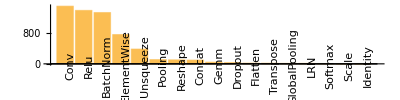

```mathematica
BarChart[layerTypes,ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[layerTypes]]),
AspectRatio->1/4,ImageSize->Scaled[0.75]]
```

```mathematica
ExportString[Normal[layerTypes]/.Rule->List,"CSV"]//CopyToClipboard
```

## A look at ElementWise

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Lookup[Select[Import[file,"RawJSON"],#["type"]==="ElementWise"&],"input_dimensions"];
net,
{file,files}
];
```

```mathematica
nets
```

{<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,748,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>}
 |  |  |  |

## Move look at ElementWise

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Select[Import[file,"RawJSON"],#["type"]==="ElementWise"&];
net,
{file,files}
];
```

```mathematica
nets[[1]]
```

<|name→_minusscalar0,type→ElementWise,inputs→{id,scalar_op2},outputs→{_minusscalar0},input_dimensions→<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>|>

```mathematica
nets
```

{<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,<|input_shapes→{{1,3,112,112},{1}},output_shapes→{{1,3,112,112}}|>,748,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>,<|input_shapes→{{1,544,7,7},{1,544,7,7}},output_shapes→{{1,544,7,7}}|>}
 |  |  |  |

## A look at GEMM

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
nets=Catenate@Table[
net=Lookup[Select[Import[file,"RawJSON"],ToUpperCase[#["type"]]==="GEMM"||ToUpperCase[#["type"]]==="MATMUL"&],"input_dimensions"];
net,
{file,files}
];
```

```mathematica
nets
```

{<|input_shapes→{{1,512,7,7},{512,25088},{512}},output_shapes→{{1,512}}|>,<|input_shapes→{{1,9216},{4096,9216},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,9216},{4096,9216},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,9216},{4096,9216},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{200,4096},{200}},output_shapes→{{1,200}}|>,<|input_shapes→{{1,4096},{4096,1024}},output_shapes→{{1,1024}}|>,<|input_shapes→{{1,1024},{1024,1024}},output_shapes→{{1,1024}}|>,<|input_shapes→{{1,1024},{1024,8}},output_shapes→{{1,8}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,256},{256,10}},output_shapes→{{1,10}}|>,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,512,1,1},{1000,512},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,512},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{0,-1},{1000,512},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,512,1,1},{1000,512},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>,<|input_shapes→{{1,544},{1000,544},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,512,7,7},{4096,25088},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{4096,4096},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1000,4096},{1000}},output_shapes→{{1,1000}}|>,<|input_shapes→{{1,18432},{4096,18432},{4096}},output_shapes→{{1,4096}}|>,<|input_shapes→{{1,4096},{1024,4096},{1024}},output_shapes→{{1,1024}}|>,<|input_shapes→{{1,1024},{1000,1024},{1000}},output_shapes→{{1,1000}}|>}

## % of layers common between networks

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
```

```mathematica
nets=Catenate@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
net,
{file,files}
];
netLayers=Counts[nets];
N[Length[netLayers]/Total[Values[netLayers]]]
```

0.179006

```mathematica
layerTypes=Reverse@Sort@Counts[Lookup[nets,"type"]];
BarChart[layerTypes,ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[layerTypes]]),
AspectRatio->1/4,ImageSize->Scaled[0.75]]
```

-Graphics-

```mathematica
layerTypes
```

<|Conv→1481,Relu→1372,BatchNorm→1317,ElementWise→752,Unsqueeze→380,Pooling→109,Reshape→103,Concat→97,Gemm→43,Dropout→32,Flatten→18,Transpose→16,GlobalPooling→12,LRN→12,Softmax→8,Scale→1,Identity→1|>

```mathematica
ExportString[Normal[layerTypes]/.Rule->List,"CSV"]//CopyToClipboard
```

```mathematica
Keys[layerTypes]
```

{Conv,Relu,BatchNorm,ElementWise,Unsqueeze,Pooling,Reshape,Concat,Gemm,Dropout,Flatten,Transpose,GlobalPooling,LRN,Softmax,Scale,Identity}

```mathematica
Reverse@Sort[netLayers]
```

<|<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,14,14},{256},{256},{256},{256}},output_shapes→{{1,256,14,14},{256},{256},{256},{256}}|>|>→383,1028,<|type→Identity,input_dimensions→<|input_shapes→{{1,3,112,112}},output_shapes→{{1,3,112,112}}|>|>→1|>
 |  |  |  |

```mathematica
percs2=Association@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
FileBaseName[file]->net,
{file,files}
];
```

```mathematica
Keys[percs2]
```

{ArcFace,BVLC_AlexNet,BVLC_CaffeNet,BVLC_GoogleNet,BVLC_RCNN_ILSVRC13,DenseNet-121,DUC,Emotion-FerPlus,Inception-v1,Inception-v2,MNIST,MobileNet-v2,ResNet018-v1,ResNet018-v2,ResNet034-v1,ResNet034-v2,ResNet050-v1,ResNet050-v2,ResNet101-v1,ResNet101-v2,ResNet152-v1,ResNet152-v2,Shufflenet,Squeezenet-v1.1,Tiny_YOLO-v2,VGG16-BN,VGG16,VGG19-BN,VGG19,Zfnet512}

```mathematica
Length@Counts@Catenate[Table[Lookup[e,{"type","input_dimensions"}],{e,percs2}]]
```

1030

```mathematica
69.0/1229
```

0.0561432

```mathematica
Length@Counts@Catenate[Table[Lookup[e,{"type","input_dimensions"}],{e,Values@KeySelect[percs2,StringContainsQ[ToLowerCase[#],"resnet"]&&StringContainsQ[ToLowerCase[#],"v1"]&]}]]
```

60

```mathematica
N@(Length@Counts@Lookup[percs2["ResNet152-v1"],{"type","input_dimensions"}])/(Length@Lookup[percs2["ResNet152-v1"],{"type","input_dimensions"}])
```

0.0912621

```mathematica
Lookup[percs2["ResNet101-v1"],{"type","input_dimensions"}]
```

{{Conv,<|input_shapes→{{1,3,224,224},{64,3,7,7}},output_shapes→{{1,64,112,112}}|>},{BatchNorm,<|input_shapes→{{1,64,112,112},{64},{64},{64},{64}},output_shapes→{{1,64,112,112},{64},{64},{64},{64}}|>},342,{Gemm,<|input_shapes→{{1,2048,1,1},{1000,2048},{1000}},output_shapes→{{1,1000}}|>}}
 |  |  |  |

```mathematica
Grid[
Normal[Reverse@Sort@Counts[Table[
{e[[1]],e[[2]]["input_shapes"][[1]]},
{e,Lookup[percs2["ResNet50-v1"],{"type","input_dimensions"}]}
]]]/.Rule->List,Frame->All]
```

{Conv,{1,256,14,14}} | 12
{Relu,{1,256,14,14}} | 12
{BatchNorm,{1,256,14,14}} | 12
{Conv,{1,128,28,28}} | 8
{Relu,{1,128,28,28}} | 8
{BatchNorm,{1,128,28,28}} | 8
{Conv,{1,64,56,56}} | 8
{Conv,{1,1024,14,14}} | 7
{BatchNorm,{1,1024,14,14}} | 7
{Conv,{1,512,7,7}} | 6
{Relu,{1,512,7,7}} | 6
{BatchNorm,{1,512,7,7}} | 6
{Relu,{1,1024,14,14}} | 6
{ElementWise,{1,1024,14,14}} | 6
{Relu,{1,64,56,56}} | 6
{BatchNorm,{1,64,56,56}} | 6
{Conv,{1,512,28,28}} | 5
{BatchNorm,{1,512,28,28}} | 5
{BatchNorm,{1,2048,7,7}} | 4
{Relu,{1,512,28,28}} | 4
{ElementWise,{1,512,28,28}} | 4
{Conv,{1,256,56,56}} | 4
{BatchNorm,{1,256,56,56}} | 4
{Relu,{1,2048,7,7}} | 3
{ElementWise,{1,2048,7,7}} | 3
{Relu,{1,256,56,56}} | 3
{ElementWise,{1,256,56,56}} | 3
{Conv,{1,2048,7,7}} | 2
{Gemm,{1,2048,1,1}} | 1
{Flatten,{1,2048,1,1}} | 1
{GlobalPooling,{1,2048,7,7}} | 1
{Pooling,{1,64,112,112}} | 1
{Relu,{1,64,112,112}} | 1
{BatchNorm,{1,64,112,112}} | 1
{Conv,{1,3,224,224}} | 1

```mathematica
Grid[
Normal[Reverse@Sort@Counts[Table[
{e[[1]],e[[2]]["input_shapes"][[1]]},
{e,Lookup[percs2["ResNet101-v1"],{"type","input_dimensions"}]}
]]]/.Rule->List,Frame->All]
```

{Conv,{1,256,14,14}} | 46
{Relu,{1,256,14,14}} | 46
{BatchNorm,{1,256,14,14}} | 46
{Conv,{1,1024,14,14}} | 24
{BatchNorm,{1,1024,14,14}} | 24
{Relu,{1,1024,14,14}} | 23
{ElementWise,{1,1024,14,14}} | 23
{Conv,{1,128,28,28}} | 8
{Relu,{1,128,28,28}} | 8
{BatchNorm,{1,128,28,28}} | 8
{Conv,{1,64,56,56}} | 8
{Conv,{1,512,7,7}} | 6
{Relu,{1,512,7,7}} | 6
{BatchNorm,{1,512,7,7}} | 6
{Relu,{1,64,56,56}} | 6
{BatchNorm,{1,64,56,56}} | 6
{Conv,{1,512,28,28}} | 5
{BatchNorm,{1,512,28,28}} | 5
{BatchNorm,{1,2048,7,7}} | 4
{Relu,{1,512,28,28}} | 4
{ElementWise,{1,512,28,28}} | 4
{Conv,{1,256,56,56}} | 4
{BatchNorm,{1,256,56,56}} | 4
{Relu,{1,2048,7,7}} | 3
{ElementWise,{1,2048,7,7}} | 3
{Relu,{1,256,56,56}} | 3
{ElementWise,{1,256,56,56}} | 3
{Conv,{1,2048,7,7}} | 2
{Gemm,{1,2048,1,1}} | 1
{Flatten,{1,2048,1,1}} | 1
{GlobalPooling,{1,2048,7,7}} | 1
{Pooling,{1,64,112,112}} | 1
{Relu,{1,64,112,112}} | 1
{BatchNorm,{1,64,112,112}} | 1
{Conv,{1,3,224,224}} | 1

## % of layers not supported by CUDNN|Scope

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
```

```mathematica
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
notSupported=Counts@Flatten@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
notsupported=Select[Lookup[net,"type"],!KeyExistsQ[cudnnSupported,#]&];
notsupported,
{file,files}
];
```

```mathematica
notSupported
```

<|Reshape→103,Flatten→18,Concat→97,Unsqueeze→380,GlobalPooling→12,Transpose→16,Scale→1|>

## % of layers supported by CUDNN|Scope

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats";
files=FileNames["*.json",dir];
```

```mathematica
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"GlobalPooling"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
layerPerc=Association@Table[
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
supported=Select[Lookup[net,"type"],KeyExistsQ[cudnnSupported,#]&];
FileBaseName[file]->N[Length[supported]/Length[net]],
{file,files}
];
```

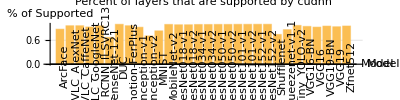

```mathematica
BarChart[
KeyValueMap[Function[{key,val},Tooltip[val,val]],layerPerc],
ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[layerPerc]]),
AxesLabel->{"Model",Rotate["% of Supported",90Degree]},
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
PlotLabel->"Percent of layers that are supported by cudnn",
AspectRatio->1/4,
ImageSize->Scaled[0.75]
]
```

```mathematica
ExportString[MapIndexed[{#2[[1]],100*Round[#1,0.0001]}&,Values@layerPerc],"CSV"]//CopyToClipboard
```

## layers no supported by CUDNN|Scope for inception-v2

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/inception-v2.json";
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"GlobalPooling"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
notsupported=Counts@Select[Lookup[net,"type"],!KeyExistsQ[cudnnSupported,#]&];
```

```mathematica
Length[Lookup[net,"type"]]
```

509

```mathematica
1-(N@Total[Values[notsupported]]/Length[Lookup[net,"type"]])
```

0.707269

```mathematica
notsupported
```

<|Unsqueeze→138,Concat→10,Reshape→1|>

```mathematica
138/509.0
```

0.27112

## layers no supported by CUDNN|Scope for densenet

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/DenseNet-121.json";
cudnnSupported=<|"Relu"->True,"BatchNorm"->True,"Conv"->True,"Dropout"->True,"Pooling"->True,"LRN"->True,"GlobalPooling"->True,"Identity"->True,"Softmax"->True,"Gemm"->True,"MatMul"->True,"ElementWise"->True|>;
net=KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&];
notsupported=Counts@Select[Lookup[net,"type"],!KeyExistsQ[cudnnSupported,#]&];
```

```mathematica
Length[Lookup[net,"type"]]
```

910

```mathematica
1-(N@Total[Values[notsupported]]/Length[Lookup[net,"type"]])
```

0.67033

```mathematica
notsupported
```

<|Unsqueeze→242,Concat→58|>

```mathematica
242/910.0
```

0.265934

## Model List

```mathematica
ii=1;
idMap=AssociationThread[Sort[Keys[percs]]->Range[Length[layerPerc]]];
ExportString[KeyValueMap[Function[{key,val},{ii++,Round[100*val,0.1]}],layerPerc],"CSV"]//CopyToClipboard
```

Keys::invrl: The argument percs is not a valid Association or a list of rules.

```mathematica
percs=Association@Table[
net=Counts[KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
FileBaseName[file]->N[Length[net]/Total[Values[net]]],
{file,files}
];
```

```mathematica
Keys[percs]
```

{ArcFace,BVLC_AlexNet,BVLC_CaffeNet,BVLC_GoogleNet,BVLC_RCNN_ILSVRC13,DenseNet-121,DUC,Emotion-FerPlus,Inception-v1,Inception-v2,MNIST,MobileNet-v2,ResNet018-v1,ResNet018-v2,ResNet034-v1,ResNet034-v2,ResNet050-v1,ResNet050-v2,ResNet101-v1,ResNet101-v2,ResNet152-v1,ResNet152-v2,Shufflenet,Squeezenet-v1.1,Tiny_YOLO-v2,VGG16-BN,VGG16,VGG19-BN,VGG19,Zfnet512}

```mathematica
ii=1;
idMap=AssociationThread[Sort[Keys[percs]]->Range[Length[percs]]];
ExportString[KeyValueMap[Function[{key,val},{ii++,Round[100*val,0.1]}],percs],"CSV"]//CopyToClipboard
```

```mathematica
idMap/@Keys[percs]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,27,26,29,28,30}

```mathematica
ii=1;
StringRiffle[Map[Function[{key},StringJoin[{ToString[ii++]," & ",StringTrim[StringReplace[ToLowerCase@key,"_"->"-"],"\""], " & ", "IC", " & ","  0 &", "\\cite{xxx}"}]],Sort[Keys[percs]]],"\\\\\n"]//CopyToClipboard
```

```mathematica
ii=1;
ExportString[KeyValueMap[Function[{key,val},{ii++,100*val}],percs],"CSV"]//CopyToClipboard
```

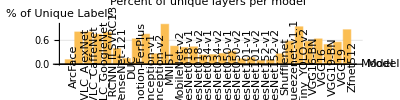

```mathematica
BarChart[
KeyValueMap[Function[{key,val},Tooltip[val,key]],percs],
ChartLabels->(Rotate[#,90Degree]&/@Keys[Normal[percs]]),
AxesLabel->{"Model",Rotate["% of Unique Labels",90Degree]},
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
PlotLabel->"Percent of unique layers per model",
AspectRatio->1/4,
ImageSize->Scaled[0.75]
]
```

```mathematica
files
```

```mathematica
file=SelectFirst[files,StringContainsQ["ResNet152-v2"]]
```

/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/ResNet152-v2.json

```mathematica
net=Counts[KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
N[Length[net]]
```

56.

```mathematica
Total[Values[net]]
```

514

```mathematica
net
```

<|<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,3,224,224},{3},{3},{3},{3}},output_shapes→{{1,3,224,224},{3},{3},{3},{3}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,3,224,224},{64,3,7,7}},output_shapes→{{1,64,112,112}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,64,112,112},{64},{64},{64},{64}},output_shapes→{{1,64,112,112},{64},{64},{64},{64}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,64,112,112}},output_shapes→{{1,64,112,112}}|>|>→1,<|type→Pooling,input_dimensions→<|input_shapes→{{1,64,112,112}},output_shapes→{{1,64,56,56}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,64,56,56},{64},{64},{64},{64}},output_shapes→{{1,64,56,56},{64},{64},{64},{64}}|>|>→7,<|type→Relu,input_dimensions→<|input_shapes→{{1,64,56,56}},output_shapes→{{1,64,56,56}}|>|>→7,<|type→Conv,input_dimensions→<|input_shapes→{{1,64,56,56},{64,64,1,1}},output_shapes→{{1,64,56,56}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,64,56,56},{64,64,3,3}},output_shapes→{{1,64,56,56}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,64,56,56},{256,64,1,1}},output_shapes→{{1,256,56,56}}|>|>→4,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,256,56,56},{1,256,56,56}},output_shapes→{{1,256,56,56}}|>|>→3,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,56,56},{256},{256},{256},{256}},output_shapes→{{1,256,56,56},{256},{256},{256},{256}}|>|>→3,<|type→Relu,input_dimensions→<|input_shapes→{{1,256,56,56}},output_shapes→{{1,256,56,56}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,56,56},{64,256,1,1}},output_shapes→{{1,64,56,56}}|>|>→2,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,56,56},{128,256,1,1}},output_shapes→{{1,128,56,56}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,128,56,56},{128},{128},{128},{128}},output_shapes→{{1,128,56,56},{128},{128},{128},{128}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,128,56,56}},output_shapes→{{1,128,56,56}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,128,56,56},{128,128,3,3}},output_shapes→{{1,128,28,28}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,128,28,28},{128},{128},{128},{128}},output_shapes→{{1,128,28,28},{128},{128},{128},{128}}|>|>→15,<|type→Relu,input_dimensions→<|input_shapes→{{1,128,28,28}},output_shapes→{{1,128,28,28}}|>|>→15,<|type→Conv,input_dimensions→<|input_shapes→{{1,128,28,28},{512,128,1,1}},output_shapes→{{1,512,28,28}}|>|>→8,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,56,56},{512,256,1,1}},output_shapes→{{1,512,28,28}}|>|>→1,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,512,28,28},{1,512,28,28}},output_shapes→{{1,512,28,28}}|>|>→8,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,512,28,28},{512},{512},{512},{512}},output_shapes→{{1,512,28,28},{512},{512},{512},{512}}|>|>→8,<|type→Relu,input_dimensions→<|input_shapes→{{1,512,28,28}},output_shapes→{{1,512,28,28}}|>|>→8,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,28,28},{128,512,1,1}},output_shapes→{{1,128,28,28}}|>|>→7,<|type→Conv,input_dimensions→<|input_shapes→{{1,128,28,28},{128,128,3,3}},output_shapes→{{1,128,28,28}}|>|>→7,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,28,28},{256,512,1,1}},output_shapes→{{1,256,28,28}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,28,28},{256},{256},{256},{256}},output_shapes→{{1,256,28,28},{256},{256},{256},{256}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,256,28,28}},output_shapes→{{1,256,28,28}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,28,28},{256,256,3,3}},output_shapes→{{1,256,14,14}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,256,14,14},{256},{256},{256},{256}},output_shapes→{{1,256,14,14},{256},{256},{256},{256}}|>|>→71,<|type→Relu,input_dimensions→<|input_shapes→{{1,256,14,14}},output_shapes→{{1,256,14,14}}|>|>→71,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,14,14},{1024,256,1,1}},output_shapes→{{1,1024,14,14}}|>|>→36,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,28,28},{1024,512,1,1}},output_shapes→{{1,1024,14,14}}|>|>→1,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,1024,14,14},{1,1024,14,14}},output_shapes→{{1,1024,14,14}}|>|>→36,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,1024,14,14},{1024},{1024},{1024},{1024}},output_shapes→{{1,1024,14,14},{1024},{1024},{1024},{1024}}|>|>→36,<|type→Relu,input_dimensions→<|input_shapes→{{1,1024,14,14}},output_shapes→{{1,1024,14,14}}|>|>→36,<|type→Conv,input_dimensions→<|input_shapes→{{1,1024,14,14},{256,1024,1,1}},output_shapes→{{1,256,14,14}}|>|>→35,<|type→Conv,input_dimensions→<|input_shapes→{{1,256,14,14},{256,256,3,3}},output_shapes→{{1,256,14,14}}|>|>→35,<|type→Conv,input_dimensions→<|input_shapes→{{1,1024,14,14},{512,1024,1,1}},output_shapes→{{1,512,14,14}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,512,14,14},{512},{512},{512},{512}},output_shapes→{{1,512,14,14},{512},{512},{512},{512}}|>|>→1,<|type→Relu,input_dimensions→<|input_shapes→{{1,512,14,14}},output_shapes→{{1,512,14,14}}|>|>→1,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,14,14},{512,512,3,3}},output_shapes→{{1,512,7,7}}|>|>→1,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,512,7,7},{512},{512},{512},{512}},output_shapes→{{1,512,7,7},{512},{512},{512},{512}}|>|>→5,<|type→Relu,input_dimensions→<|input_shapes→{{1,512,7,7}},output_shapes→{{1,512,7,7}}|>|>→5,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,7,7},{2048,512,1,1}},output_shapes→{{1,2048,7,7}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,1024,14,14},{2048,1024,1,1}},output_shapes→{{1,2048,7,7}}|>|>→1,<|type→ElementWise,input_dimensions→<|input_shapes→{{1,2048,7,7},{1,2048,7,7}},output_shapes→{{1,2048,7,7}}|>|>→3,<|type→BatchNorm,input_dimensions→<|input_shapes→{{1,2048,7,7},{2048},{2048},{2048},{2048}},output_shapes→{{1,2048,7,7},{2048},{2048},{2048},{2048}}|>|>→3,<|type→Relu,input_dimensions→<|input_shapes→{{1,2048,7,7}},output_shapes→{{1,2048,7,7}}|>|>→3,<|type→Conv,input_dimensions→<|input_shapes→{{1,2048,7,7},{512,2048,1,1}},output_shapes→{{1,512,7,7}}|>|>→2,<|type→Conv,input_dimensions→<|input_shapes→{{1,512,7,7},{512,512,3,3}},output_shapes→{{1,512,7,7}}|>|>→2,<|type→GlobalPooling,input_dimensions→<|input_shapes→{{1,2048,7,7}},output_shapes→{{1,2048,1,1}}|>|>→1,<|type→Reshape,input_dimensions→<|input_shapes→{{1,2048,1,1},{0,-1}},output_shapes→{{0,-1}}|>|>→1,<|type→Gemm,input_dimensions→<|input_shapes→{{0,-1},{1000,2048},{1000}},output_shapes→{{0,1000}}|>|>→1|>

```mathematica
net=Counts[KeyDrop[#,{"inputs","outputs","name"}]&/@Select[Import[file,"RawJSON"],#["type"]=!="ConstantInput"&]];
N[Length[net]]
```

56.

## CUDNN Heuristic divergence

typedef enum {
     CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM         = 0,
     CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_PRECOMP_GEMM = 1,
     CUDNN_CONVOLUTION_FWD_ALGO_GEMM                  = 2,
     CUDNN_CONVOLUTION_FWD_ALGO_DIRECT                = 3,
     CUDNN_CONVOLUTION_FWD_ALGO_FFT                   = 4,
     CUDNN_CONVOLUTION_FWD_ALGO_FFT_TILING            = 5,
     CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD              = 6,
     CUDNN_CONVOLUTION_FWD_ALGO_WINOGRAD_NONFUSED     = 7,
     CUDNN_CONVOLUTION_FWD_ALGO_COUNT                 = 8
 } cudnnConvolutionFwdAlgo_t;

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/v100/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
nonAdvised={First[MinimalBy[#,#["real_time"]&]],SelectFirst[#,#["convolution_algorithm"]===#["advised_convolution_algorithm"]&]}&/@GroupBy[convLayers,Lookup[#,{"input[0]","input[1]","input[2]","input[3]","filter_count","filter_height","filter_width","pad_height","pad_width","stride_height","stride_width","dilation_height","dilation_width"}]&];
nonAdvised=KeyValueMap[Function[{key,val},If[Lookup[val[[1]],"real_time"]=!=Lookup[val[[2]],"real_time"],key->val,Nothing]],nonAdvised];
nonAdvised=Select[nonAdvised,Apply[Divide,Lookup[#[[2]],"real_time"]]<0.8&];
```

```mathematica
convAlgorithmNames=<|
-1->Missing[],
0->"ImplicitGemm",
1->"ImplicitPreCompGemm",
2->"Gemm",
3->"Direct",
4->"FFT",
5->"FFTTiling",
6->"Winograd",
7->"WinogradNonFused",
8->"Count"
|>;
shortConvAlgorithmNames=<|
-1->Missing[],
0->"IGEMM",
1->"IPGEMM",
2->"GEMM",
3->"DRCT",
4->"FFT",
5->"TFFT",
6->"WING",
7->"WINGNF",
8->"CNT"
|>;
```

```mathematica
Lookup[#,"real_time"]&/@Values[nonAdvised]
```

{{19903.5,25171.},{29871.,55871.5},{36654.,72962.2},{39669.3,81738.3},{49468.3,137342.},{11477.2,15442.7},{39903.7,92717.},{14081.7,21570.1},{15053.1,24746.5},{84375.1,115571.},{39840.5,60497.6},{16068.6,25058.1},{16691.1,25710.2},{102910.,142699.},{54943.1,74870.5},{93149.4,129359.},{16663.8,25930.7},{29980.1,56093.8},{36747.8,73042.2},{39701.5,82149.5},{49510.1,138011.},{31018.4,69813.8}}

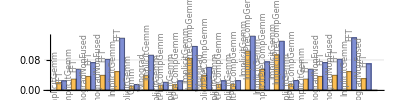

```mathematica
BarChart[
Table[Table[Labeled[j["real_time"]/10^6,Rotate[Style[convAlgorithmNames[Floor@j["convolution_algorithm"]],Gray,FontSize->8] ,90Degree],Above],{j,e}],{e,Values[nonAdvised]}],
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
BarSpacing->{0,1},
ChartLegends->{"fastest","advised"}
]
```

### normalized

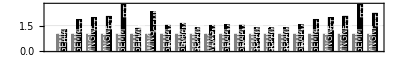

```mathematica
BarChart[
Table[
{
Labeled[1,Rotate[Style[shortConvAlgorithmNames[Floor@e[[1]]["convolution_algorithm"]],White,FontSize->8] ,90Degree],Top],
Labeled[e[[2]]["real_time"]/e[[1]]["real_time"],Rotate[Style[shortConvAlgorithmNames[Floor@e[[2]]["convolution_algorithm"]],White,FontSize->8] ,90Degree],Top]
},{e,Values[nonAdvised]}],
PlotTheme->{"FrameGrid","GrayColor"},
Ticks->{None,Automatic} ,
AspectRatio->1/6,
ChartStyle->{Gray,Black},
ImageSize->Scaled[0.75],
BarSpacing->{0,1}
]
```

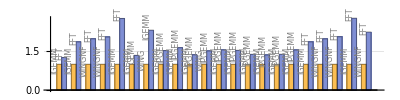

```mathematica
BarChart[
Table[
{
Labeled[1,Rotate[Style[shortConvAlgorithmNames[Floor@e[[1]]["convolution_algorithm"]],Gray,FontSize->8] ,90Degree],Above],
Labeled[e[[2]]["real_time"]/e[[1]]["real_time"],Rotate[Style[shortConvAlgorithmNames[Floor@e[[2]]["convolution_algorithm"]],Gray,FontSize->8] ,90Degree],Above]
},{e,Values[nonAdvised]}],
PlotTheme->{"Grid"},
Ticks->{None,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
BarSpacing->{0,1},
ChartLegends->{"fastest","advised"}
]
```

## Inception Module Analysis

## Batch Sizes

## Memory Copy Model

process the data

```mathematica
Pane[StringRiffle[FileNames["*json","~/code/ispass-19/data/"],"\n"],ImageSize->{Full,300},Scrollbars->True]
```

~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Coherence_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Coherence_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToPinned_flush_0.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_GPUToWC.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_HostToGPU_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_PinnedToGPU_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_PinnedToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_NUMAMemcpy_WCToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Prefetch_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_Prefetch_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Coherence_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Coherence_GPUToHostMt.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Coherence_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_Duplex_GPUGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_Duplex_GPUGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_GPUToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-2_Comm_ZeroCopy_GPUToGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Host_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Pinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_Memcpy_GPUToGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_GPUToHost_0.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_GPUToHost_flush_0.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_HostToPinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_NUMAMemcpy_HostToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Coherence_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_ZeroCopy_HostToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f37-ac922-3_Comm_ZeroCopy_HostToGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Coherence_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Coherence_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Memcpy_GPUToGPUPeer.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToPinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_GPUToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToGPU_0.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToGPU_flush_0.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToPinned_flush.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_HostToPinned.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_PinnedToGPU_flush.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_PinnedToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Prefetch_Duplex_GPUGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_Prefetch_Duplex_HostGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_GPUToHostMt.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Coherence_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_Duplex_GPUGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_Duplex_GPUGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_GPUToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_GPUToGPU_Write.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_HostToGPU_Read.json
~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_ZeroCopy_HostToGPU_Write.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_Memcpy_GPUGPUPeer.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Host_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Host.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Pinned_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Duplex_NUMAMemcpy_Pinned.json
~/code/ispass-19/data/GROUP_minsky1_Comm_Memcpy_GPUToGPUPeer.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToHost_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToHost.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToPinned_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_GPUToPinned.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToGPU_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToPinned_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToPinned.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_PinnedToGPU_flush.json
~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_PinnedToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_GPUToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_GPUToHost.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_GPUToHostMt.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Coherence_HostToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Prefetch_GPUToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Prefetch_GPUToHost.json
~/code/ispass-19/data/GROUP_minsky1_Comm_UM_Prefetch_HostToGPU.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_Duplex_GPUGPU_Read.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_Duplex_GPUGPU_Write.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_GPUToGPU_Read.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_GPUToGPU_Write.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_HostToGPU_Read.json
~/code/ispass-19/data/GROUP_minsky1_Comm_ZeroCopy_HostToGPU_Write.json

```mathematica
rawdata=Import["~/code/ispass-19/data/GROUP_cs-host-f4a-sm8_Comm_NUMAMemcpy_PinnedToGPU.json","RawJSON"]["benchmarks"];
rawdata=Import["~/code/ispass-19/data/GROUP_minsky1_Comm_NUMAMemcpy_HostToGPU.json","RawJSON"]["benchmarks"];
```

```mathematica
data=KeyValueMap[Function[{k,v},{k,Min[v[[All,2]]]}],GroupBy[Map[{Log2@#[[1]],#[[1]]/#[[2]]}&,
Select[
Lookup[rawdata,{"bytes","real_time"}],
#[[1]]>0&
]],First]];
minX=10;
maxX=Max[data[[All,1]]];
data
```

{{29.,14.507},{2.16096,9.83632×10^-6},{22.,16.1434},{-4.83904,1.42883×10^-6},{27.,15.4315},{0.160964,0.000018162},{17.,8.82299},{-9.83904,0.0000201797},{19.,12.834},{-7.83904,0.0000969247},{18.,11.0654},{-8.83904,0.0000363502},{14.,2.44309},{-12.839,1.00476×10^-6},{33.,14.1637},{6.16096,7.83795×10^-6},{12.,0.69471},{-14.839,6.8585×10^-7},{24.,14.921},{-2.83904,6.90144×10^-6},{16.,4.96134},{-10.839,3.91461×10^-6},{10.,0.17897},{-16.839,2.7329×10^-7},{8.,0.0437816},{-18.839,4.01346×10^-8},{21.,16.3883},{-5.83904,2.29228×10^-6},{28.,14.8247},{1.16096,0.0000119263},{20.,13.6647},{-6.83904,3.61836×10^-6},{23.,14.0198},{-3.83904,2.34597×10^-6},{13.,1.34881},{-13.839,9.06677×10^-7},{30.,14.383},{3.16096,0.0000103894},{15.,3.64977},{-11.839,2.37604×10^-6},{9.,0.0868238},{-17.839,6.12888×10^-8},{11.,0.356936},{-15.839,3.41425×10^-7},{32.,14.1398},{5.16096,8.70875×10^-6},{31.,14.2708},{4.16096,9.87134×10^-6},{26.,15.9191},{-0.839036,4.23482×10^-6},{25.,16.534},{-1.83904,4.36594×10^-6}}

find a formula that fits the data (this uses some “magic” to get the formula)

```mathematica
ClearAll[x];
fit=FindFormula[data,x]//FullSimplify
```

0.0351205+1/(0.0664935+20424.3 ⅇ^(-0.760606 x))

```mathematica
StringReplace[
ToString@CForm[fit/.E^(x__):>mathExp[x]],
"mathExp"->"math.Exp"
]//CopyToClipboard
```

```mathematica
TraditionalForm[fit]
```

1/(0.0664935+20424.3 ⅇ^(-0.760606 x))+0.0351205

Plots similar to the ones presented in the paper (on trimmed dataset starting at 2^10)

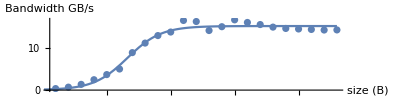

```mathematica
trimmedData=Select[data,#[[1]]>minX&];
Show[ListPlot[trimmedData,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
AxesLabel->{"size (B)","Bandwidth GB/s"}],Plot[fit,{x,minX,maxX},Filling->{2->{1}}]]
```

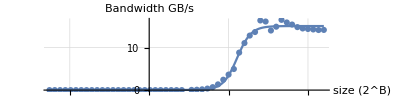

```mathematica
Show[
ListPlot[
data,
PlotTheme->"Grid",
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"size (2^B)","Bandwidth GB/s"}
],
Plot[
fit,
{x,0,maxX},
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
]
```

## CUDNN Log ResNet

```mathematica
data=Import["/tmp/cudnn.log","Text"];
```

```mathematica
funcs=Rest[
Flatten@Table[StringCases[line,"I! CuDNN (v7600) function "~~x__~~"("~~__:>x],{line,StringSplit[data,"\n"]}]
];
```

```mathematica
times=DateObject[DateList[#]]&/@Flatten@Table[StringCases[line,"i! Time: "~~x__~~" ("~~__:>x],{line,StringSplit[data,"\n"]}];
```

```mathematica
times=times-times[[1]];
```

```mathematica
durations=UnitConvert[#,"ms"]&/@(times[[2;;]]-times[[;;-2]]);
```

```mathematica
With[{ufuncs=Union[funcs]},
colorOf[func_]:=ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]
]
```

```mathematica
ListPlot[
MapThread[Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]&,{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

```mathematica
ListPlot[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize"||
#2==="cudnnDestroyTensorDescriptor",
Nothing,
Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]
]&,
{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

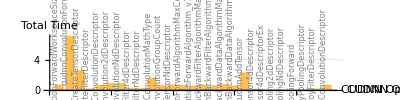

```mathematica
hist=Merge[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize"||
#2==="cudnnDestroyTensorDescriptor",
Nothing,
#2->#1
]&,
{durations,funcs}][[400;;]],
Total
];
BarChart[
KeyValueMap[
Function[{k,v},
Labeled[v,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time"}
]
```

## CUDNN Log

```mathematica
data=Import["~/cudnn.log","Text"];
```

```mathematica
funcs=Rest[
Flatten@Table[StringCases[line,"I! CuDNN (v7501) function "~~x__~~"("~~__:>x],{line,StringSplit[data,"\n"]}]
];
```

```mathematica
times=DateObject[DateList[#]]&/@Flatten@Table[StringCases[line,"i! Time: "~~x__~~" ("~~__:>x],{line,StringSplit[data,"\n"]}];
```

```mathematica
times=times-times[[1]];
```

```mathematica
durations=UnitConvert[#,"ms"]&/@(times[[2;;]]-times[[;;-2]]);
```

```mathematica
With[{ufuncs=Union[funcs]},
colorOf[func_]:=ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]
]
```

```mathematica
ListPlot[
MapThread[Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]&,{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

```mathematica
ListPlot[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]
]&,
{durations,funcs}][[400;;]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

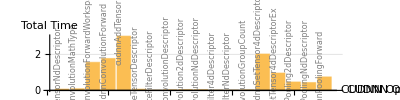

```mathematica
hist=Merge[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
#2->#1
]&,
{durations,funcs}][[400;;]],
Total
];
BarChart[
KeyValueMap[
Function[{k,v},
Labeled[v,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time"}
]
```

## CUDNN Log (Inception - Scratch)

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_log_parser/_fixtures/alexnet_cudnn.log","Text"];
```

```mathematica
funcs=Rest[
Flatten@Table[StringCases[line,"I! CuDNN (v7501) function "~~x__~~"("~~__:>x],{line,StringSplit[data,"\n"]}]
];
```

```mathematica
times=DateObject[DateList[#]]&/@Flatten@Table[StringCases[line,"i! Time: "~~x__~~" ("~~__:>x],{line,StringSplit[data,"\n"]}];
```

```mathematica
times=times-times[[1]];
```

```mathematica
durations=UnitConvert[#,"ms"]&/@(times[[2;;]]-times[[;;-2]]);
```

```mathematica
Length[durations]
```

952

```mathematica
With[{ufuncs=Union[funcs]},
colorOf[func_]:=ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]
]
```

```mathematica
ListPlot[
MapThread[Tooltip[Callout[Style[#1,colorOf[#2]],#2],#2]&,{durations,funcs}][[400;;-100]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

```mathematica
ListPlot[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
Tooltip[Callout[Style[#1,colorOf[#2]],#2],#1]
]&,
{durations,funcs}][[400;;-100]],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

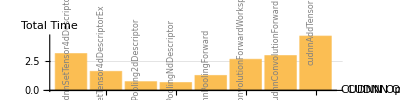

```mathematica
hist=Merge[
MapThread[
If[
#2==="cudnnGetConvolutionBackwardDataWorkspaceSize"||
#2==="cudnnGetConvolutionBackwardFilterWorkspaceSize",
Nothing,
#2->#1
]&,
{durations,funcs}][[400;;-100]],
Total
];
BarChart[
KeyValueMap[
Function[{k,v},
Labeled[v,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time"}
]
```

## CUDNN Log2 (SCRATCH)

```mathematica
data=Import["~/cudnn.log","Text"];
```

```mathematica
Select[Select[StringTrim/@StringSplit[data,"I! CuDNN (v7501) function "],#=!=""&],StringStartsQ[#,"cudnnAddTensor"]&]
```

{cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.367743 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.397321 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.447056 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.492127 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.526016 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.529206 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.529940 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.530596 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.531112 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.531631 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.532972 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.533334 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.533676 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.533916 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.534161 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.535464 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.535835 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.536175 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.536388 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.536601 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.537869 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.538235 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.538574 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.538786 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.538997 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.540237 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.540600 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.540943 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.541157 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.541364 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.542590 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.542952 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.543293 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.543508 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.543722 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.545092 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.545460 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.545849 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.546071 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.546280 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.547626 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.547987 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.548326 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.548537 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.548748 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.550006 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.550368 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.550709 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.550923 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.551135 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.552351 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.552713 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.553052 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.553263 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c300083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.553479 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14130; GPU=0; Handle=0x7f4c206fdc00; StreamId=0x7f4c300083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,1,1];
i!         strideA: type=int; val=[96,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fd400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,96,54,54];
i!         strideA: type=int; val=[279936,2916,54,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.554827 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c859fe400;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,26,26];
i!         strideA: type=int; val=[173056,676,26,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.555187 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2c000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b400000;
i! Time: 2019-06-02T18:55:31.555526 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,1,1];
i!         strideA: type=int; val=[384,1,1,1];
i!     biasData: location=dev; addr=0x7f4c17f2d000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,384,12,12];
i!         strideA: type=int; val=[55296,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c176ed600;
i! Time: 2019-06-02T18:55:31.555739 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.,cudnnAddTensor() called:
i!     handle: type=cudnnHandle_t; streamId=0x7f4c340083d0;
i!     alpha: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     biasDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,1,1];
i!         strideA: type=int; val=[256,1,1,1];
i!     biasData: location=dev; addr=0x7f4c0a9b0000;
i!     beta: type=CUDNN_DATA_FLOAT; val=1.000000;
i!     srcDestDesc: type=cudnnTensorDescriptor_t:
i!         dataType: type=cudnnDataType_t; val=CUDNN_DATA_FLOAT (0);
i!         nbDims: type=int; val=4;
i!         dimA: type=int; val=[1,256,12,12];
i!         strideA: type=int; val=[36864,144,12,1];
i!     srcDestData: location=dev; addr=0x7f4c0b200000;
i! Time: 2019-06-02T18:55:31.555950 (0d+0h+0m+6s since start)
i! Process=14023; Thread=14131; GPU=0; Handle=0x7f4c340ddba0; StreamId=0x7f4c340083d0.}

## CUDNN Log using parser (Alexnet)

```mathematica
rawdata=Select[
Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/cudnn_log_parser/_fixtures/alexnet_cudnn.csv"],
Length[#]==3&
];
rawdata=Apply[Rule,rawdata[[2;;,;;2]],{1}][[5;;-100]];
```

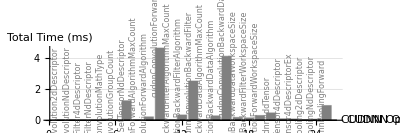

```mathematica
data=Merge[rawdata,Total];
BarChart[
KeyValueMap[
Function[{k,v},
If[StringContainsQ[k,"cudnnDestroy"]||StringContainsQ[k,"cudnnCreate"],
Nothing,
Labeled[v/12,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
]
],
data
],
ChartStyle->Gray,
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/3,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN Op","Total Time (ms)"}
]
```

```mathematica
funcs=Union[First/@rawdata];
With[{ufuncs=funcs},
colorOf[func_]:=Darker[ColorData["Atoms","ColorList"][[First@FirstPosition[ufuncs,func]]]]
];
```

```mathematica
ListPlot[
Map[If[#[[2]]<0.1||StringContainsQ[#[[1]],"cudnnDestroy"]||StringContainsQ[#[[1]],"cudnnCreate"],Nothing,Tooltip[Callout[Style[#[[2]],colorOf[#[[1]]]],#[[1]]],#[[1]]]]&,rawdata],
PlotLegends->PointLegend[Table[colorOf[f],{f,Union[funcs]}],StringTrim[#,"cudnn"]&/@Union[funcs]],
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All
]
```

-Graphics-

get the total time

```mathematica
KeyValueMap[
Function[{k,v},
If[StringContainsQ[k,"cudnnDestroy"]||StringContainsQ[k,"cudnnCreate"]||StringContainsQ[k,"cudnnGetCon"],
Nothing,
v/12
]
],
data
]//Total
```

15.4031

## Plot our recall time ResNet50-v1 Animate

```mathematica
Manipulate[
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/batchsize_"<>ToString[batchSize]<>"/Tesla_V100-SXM2-16GB/ResNet050-v1.csv","CSV"];
header=First[data];
rdata=Most[Rest[data]];
data=AssociationThread[header->#]&/@rdata;
layerData=100*(Total[Lookup[#,"RealTime(ms)"]]&/@GroupBy[data,#["LayerType"]&])/Total[Lookup[data,"RealTime(ms)"]];
PieChart[layerData,ChartLabels->Keys[layerData],PlotLabel->("Batch Size"<>ToString[batchSize])],
{batchSize,2^Range[0,4]}
]
```

## Plot our recall time ResNet50-v1

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/latency/batchsize_16/Tesla_V100-SXM2-16GB/ResNet050-v1.csv","CSV"];
header=First[data];
rdata=Most[Rest[data]];
data=AssociationThread[header->#]&/@rdata;
```

```mathematica
Total[Lookup[Select[data,#["LayerType"]==="ElementWise"&],"RealTime(ms)"]]/Total[Lookup[data,"RealTime(ms)"]]
```

0.0404341

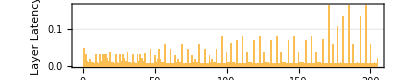

```mathematica
fig=BarChart[
MapThread[Tooltip,{Lookup[data,"RealTime(ms)"],Lookup[data,"LayerName"]}],
PlotTheme->"Grid",
AspectRatio->1/5,
Frame->True,
BarSpacing->{1,1},
FrameLabel->{Style["Layer Index",14],Style["Layer Latency",14]},
ImageSize->Scaled[0.75]
]
```

```mathematica
Dataset[data]
```

Dataset[<>]

## Plot our recall time

```mathematica
data=Import["/tmp/e.json","RawJSON"];
```

```mathematica
nameOf[elem_]:=StringSplit[elem["benchmark"]["Name"],"_FLOAT32__"][[1]];
timeOf[elem_]:=elem["benchmark"]["RealTime"];
```

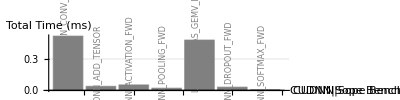

```mathematica
BarChart[
KeyValueMap[
Function[{k,v},
If[ToLowerCase[k]=="total",
Nothing,
Labeled[v/1000000,Rotate[Style[k,Gray,FontSize->8] ,90Degree],Above]
]
],
Merge[Map[nameOf[#]->timeOf[#]&,data],Total]
],
ChartStyle->Gray,
PlotTheme->{"Grid"},
Ticks->{Automatic,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75],
PlotRange->All,
AxesLabel->{"CUDNN|Sope Bench","Total Time (ms)"}
]
```

## Distribution of Conv Algorithms

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/v100/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
```

```mathematica
convAlgorithmNames=<|
-1->Missing[],
0->"ImplicitGemm",
1->"ImplicitPreCompGemm",
2->"Gemm",
3->"Direct",
4->"FFT",
5->"FFTTiling",
6->"Winograd",
7->"WinogradNonFused",
8->"Count"
|>;
```

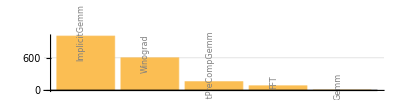

```mathematica
hist=Reverse[Sort[Counts[Lookup[convLayers,"advised_convolution_algorithm"]]]];
BarChart[
KeyValueMap[Function[{k,v},
Labeled[v,Rotate[Style[convAlgorithmNames[Floor[k]],Gray,FontSize->8] ,90Degree],Above]
],
hist
],
PlotTheme->"Grid",
Ticks->{None,Automatic} ,
AspectRatio->1/4,
ImageSize->Scaled[0.75]
]
```

## Predicting Conv Compute (all algorithms)

can we find a curve that predicts the time given some flops?

hopeless if you look at all the conv algorithms

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/v100/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
convLayers=Select[convLayers,#["predicted_flops_count"]>0&&#["advised_convolution_algorithm"]===#["convolution_algorithm"]&];
```

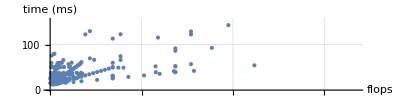

```mathematica
ListPlot[
Transpose[{Lookup[convLayers,"predicted_advised_flops_count"],Lookup[convLayers,"real_time"]/1000}],
AxesLabel->{"flops","time (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]
]
```

## Predicting Conv Compute (Implicit Gemm)

can we find a curve that predicts the time given some flops?

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/k80/1.json";
convLayers=Select[Import[file,"RawJSON"]["benchmarks"],StringContainsQ[#["name"],"CONV_FWD"(*"CONV_BWD_FILTER"*)]&&MissingQ[#["error_occurred"]]&];
convLayers=Select[convLayers,#["predicted_flops_count"]>0&&#["advised_convolution_algorithm"]===0.&];
```

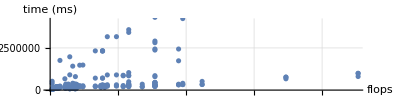

```mathematica
ListPlot[
Transpose[{Lookup[convLayers,"predicted_advised_flops_count"],Lookup[convLayers,"real_time"]}],
AxesLabel->{"flops","time (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]
]
```

```mathematica
nCrossValidation[dataset0_,n_]:=Module[{dataset=RandomSample[dataset0], trainSet,testSet,size,i,res={},c},size=IntegerPart[Length[dataset]/n];
For[i=0,i<n,i++,trainSet=Join[dataset[[1;;i*size]],dataset[[(i+1)*size+1;;]]];
testSet=dataset[[i*size+1;;(i+1)*size]];
AppendTo[res,<|"train"->trainSet,"test"->testSet|>]
];
res
]
```

```mathematica
info=Table[
<|
"flops"->Lookup[layer,"predicted_advised_flops_count"],
"time"->Quantity[Lookup[layer,"real_time"],"ms"]
|>,
{layer,convLayers}
];
```

```mathematica
nCross=nCrossValidation[info,5];
```

### Using nearest (a simple example)

```mathematica
trinfo=nCross[[1]]["train"];
nfinfo=Apply[Rule,Lookup[trinfo,{"flops","time"}],{1}];
train=Association[nfinfo];
nf=Nearest[Keys[train]]
```

NearestFunction[…]

```mathematica
test=nCross[[1]]["test"];
```

```mathematica
t1=test[[1]]
```

<|flops→8.30669×10^6,time→28922.2 ms|>

```mathematica
f=nf[t1["flops"],4];
AssociationThread[f->Lookup[train,f]]
```

<|8.42957×10^6→119362. ms,8.02816×10^6→115938. ms,8.83098×10^6→123595. ms,7.66771×10^6→137408. ms|>

```mathematica
closestFlops=nf[t1[[1]],1][[1]];
closestTime=Lookup[train,closestFlops]
```

119362. ms

```mathematica
testFlop=t1["flops"];
```

```mathematica
<|"closestFlops"->closestFlops,
"closestTime"->closestTime,
"targetFlop"->targetFlop,
"targetTime"->t1[[1]]
|>
```

<|closestFlops→8.42957×10^6,closestTime→119362. ms,targetFlop→28922.2,targetTime→8.30669×10^6|>

```mathematica
closestTime*(targetFlop/closestFlops)
```

409.537 ms

### Using nearest (full example)

```mathematica
trinfo=nCross[[1]]["train"];
nfinfo=Apply[Rule,Lookup[trinfo,{"flops","time"}],{1}];
train=Association[nfinfo];
nf=Nearest[Keys[train]]
```

NearestFunction[…]

```mathematica
testInstances=nCross[[1]]["test"];
testFlops=Lookup[testInstances,"flops"];
testActual=Lookup[testInstances,"time"];
closest=Flatten[nf[testFlops,1]];
predicted=Lookup[train,closest]*(closest/testFlops);
```

formula is predictedTime=predictedFlops closestTime/closestFlops

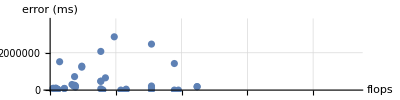

```mathematica
ListPlot[MapThread[List,{testFlops,Abs[predicted-testActual]}],
AxesLabel->{"flops","error (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]]
```

### Using gradient boosting

```mathematica
predictionData=Rule@@Transpose[Values[nCross[[1]]["train"]]];
```

```mathematica
pred=Predict[predictionData,Method->"GradientBoostedTrees"]
```

PredictorFunction[…]

```mathematica
testInstances=nCross[[1]]["test"];
testFlops=Lookup[testInstances,"flops"];
testTimes=Lookup[testInstances,"time"];
```

```mathematica
Abs[testTimes-(pred/@testFlops)][[;;10]]
```

{532251. ms,618728. ms,3.99049×10^7 ms,682942. ms,173082. ms,1.32925×10^6 ms,2.93553×10^6 ms,473687. ms,439026. ms,212375. ms}

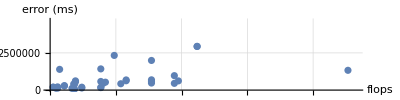

```mathematica
ListPlot[Transpose[{testFlops,Abs[testTimes-(pred/@testFlops)]}],
AxesLabel->{"flops","error (ms)"},
AspectRatio->1/4,
PlotTheme->"Grid",
ImageSize->Scaled[0.75]]
```

## Obfuscation

```mathematica
net=NetModel["Inception V1 Trained on ImageNet Competition Data"];
net=NetFlatten[net];
layers=net[[All]];
```

```mathematica
layers[[1]]
```

ConvolutionLayer[<>]

```mathematica
layerInfos=Select[
Table[
Prepend[
Association[
KeyValueMap[
Function[{k,v},
k[[1]]->v
],
NetInformation[layer,"ArraysDimensions"]
]],
"Type"->Head[layer]
],
{layer,layers}
],
KeyExistsQ["Weights"]
];
```

```mathematica
weightsData=GroupBy[Select[Union[Lookup[layerInfos,"Weights"]],Length[#]>2&],Take[#,-3]&]
```

<|{192,1,1}→{{16,192,1,1},{32,192,1,1},{64,192,1,1},{96,192,1,1}},{480,1,1}→{{16,480,1,1},{64,480,1,1},{96,480,1,1},{192,480,1,1}},{512,1,1}→{{24,512,1,1},{32,512,1,1},{64,512,1,1},{112,512,1,1},{128,512,1,1},{144,512,1,1},{160,512,1,1}},{16,5,5}→{{32,16,5,5},{48,16,5,5}},{256,1,1}→{{32,256,1,1},{64,256,1,1},{128,256,1,1}},{528,1,1}→{{32,528,1,1},{128,528,1,1},{160,528,1,1},{256,528,1,1}},{832,1,1}→{{32,832,1,1},{48,832,1,1},{128,832,1,1},{160,832,1,1},{192,832,1,1},{256,832,1,1},{384,832,1,1}},{3,7,7}→{{64,3,7,7}},{24,5,5}→{{64,24,5,5}},{32,5,5}→{{64,32,5,5},{96,32,5,5},{128,32,5,5}},{64,1,1}→{{64,64,1,1}},{48,5,5}→{{128,48,5,5}},{96,3,3}→{{128,96,3,3},{208,96,3,3}},{64,3,3}→{{192,64,3,3}},{128,3,3}→{{192,128,3,3},{256,128,3,3}},{112,3,3}→{{224,112,3,3}},{144,3,3}→{{288,144,3,3}},{160,3,3}→{{320,160,3,3}},{192,3,3}→{{384,192,3,3}}|>

```mathematica
Map[First,
weightsData,
{2}
]
```

<|{192,1,1}→{16,32,64,96},{480,1,1}→{16,64,96,192},{512,1,1}→{24,32,64,112,128,144,160},{16,5,5}→{32,48},{256,1,1}→{32,64,128},{528,1,1}→{32,128,160,256},{832,1,1}→{32,48,128,160,192,256,384},{3,7,7}→{64},{24,5,5}→{64},{32,5,5}→{64,96,128},{64,1,1}→{64},{48,5,5}→{128},{96,3,3}→{128,208},{64,3,3}→{192},{128,3,3}→{192,256},{112,3,3}→{224},{144,3,3}→{288},{160,3,3}→{320},{192,3,3}→{384}|>

## Using our layer information data to only look at inner loops

-Graphics-

essentially, if we take N as fixed, then we can just say that a layer is pK with p as a parameter. So we can ignore k and decrease the number of unique layers

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/layer_stats/inception-v1.json","RawJSON"];
```

```mathematica
shapeinfo=Map[Most,Lookup[Lookup[Select[data,#["type"]==="Conv"&],"input_dimensions"],"input_shapes"]];
```

```mathematica
N[Length[Union[shapeinfo]]/Length[shapeinfo]]
```

0.859649

```mathematica
tshapeinfo=Map[
{#[[1,2;;]],#[[2,2;;]]}&,
shapeinfo
];
```

```mathematica
N[Length[Union[tshapeinfo]]/Length[shapeinfo]]
```

0.438596

## Theoretical vs Predicted flops

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
algorithms={"ImplicitGemm",
"ImplicitPreCompGemm",
"Gemm",
"Direct",
"FFT",
"FFTTiling",
"Winograd",
"WinogradNonFused"};
shortenLabel["ImplicitPreCompGemm"]:="ImplicitGemm";
shortenLabel[s_]:=s;
```

This plot compares the algorithm against the theoretical flops

```mathematica
<<GeneralUtilities`
```

```mathematica
data=Import["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/v100/16/ResNet050-v1.json","RawJSON"];
data=Select[data,#["layer"]["operator_type"]==="Conv"&];
```

```mathematica
info=Table[
time=elem["benchmark"];
If[MissingQ[time]||time["convolution_algorithm"]=!=time["advised_convolution_algorithm"]||time["predicted_flops"]<10,
Nothing,
Labeled[{
Tooltip[
v100PeekGflop*time["RealTime"]/10.0^6,
InformationPanel["configuration",Normal[time]]
],
Tooltip[
time["predicted_flops"]/10.0^9,
InformationPanel["configuration",Normal[time]]
]
},
Rotate[Style[shortenLabel[time["convolution_algorithm"]],Gray,FontSize->8],90Degree],
Above
]
],
{elem,data}
];
```

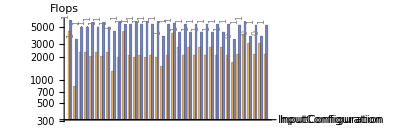

```mathematica
BarChart[info,
Ticks->{None,Automatic},
ScalingFunctions->"Log",
BarSpacing->{0,1},
AspectRatio->1/3,
ImageSize->Scaled[0.75],
AxesLabel->{"InputConfiguration","Flops"},
ChartLegends->{"measured","predicted"}]
```

Each group represents an input configuration. The y axis is the flops it takes to compute the task (the actual flops are ones that are measured and the predicted and the ones computed)

```mathematica
ndata=info/.Tooltip[x_,__]:>x/.Labeled[x_,__]:>x
```

{{4382.14,6032.45},{835.996,3441.74},{2323.05,4954.32},{2323.05,4954.32},{2056.88,5595.43},{2323.05,4954.32},{2056.88,5595.43},{2323.05,4954.32},{1319.12,4362.39},{1997.76,5761.04},{4303.36,5348.91},{2125.42,5414.98},{1997.76,5761.04},{2125.42,5414.98},{1997.76,5761.04},{2125.42,5414.98},{1997.76,5761.04},{1527.65,3766.93},{2134.09,5393.01},{4133.33,5568.95},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{2701.47,4260.33},{2134.09,5393.01},{1692.71,3399.61},{2189.6,5256.27},{3998.33,5756.99},{3045.7,3778.82},{2189.6,5256.27},{3045.7,3778.82},{2189.6,5256.27}}

```mathematica
Max[ndata]
```

6032.45

```mathematica
ExportString[Table[Prepend[ndata[[ii]],ii],{ii,Length[ndata]}],"CSV"]//CopyToClipboard
```

### Normalized

```mathematica
Max[ndata[[All,2]]/ndata[[All,1]]]
```

4.11693

```mathematica
ExportString[Table[Prepend[{1,ndata[[ii,2]]/ndata[[ii,1]]},ii],{ii,Length[ndata]}],"CSV"]//CopyToClipboard
```

## Total Time for batchsize 1 on v100

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_1/Tesla_V100-SXM2-16GB/";
files=FileNames["*.json",dir];
nets=Table[
net=Import[file,"RawJSON"];
totalEntry=SelectFirst[net,Function[{elem},KeyExistsQ[elem,"benchmark"]&&Lookup[elem["benchmark"],"Name",$Failed]==="Total"]];
{FileBaseName[file],totalEntry["benchmark"]["RealTime"]/10.0^6},
{file,files}
];
```

```mathematica
ExportString[nets,"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]
```

9.600726
0.5685669999999999
0.569263
3.621218
0.543295
9.754686
164.900007
0.97136
3.604634
5.763496
0.08857899999999999
1.975898
1.803529
1.8276109999999999
3.336483
3.360565
4.726749
4.765897
9.175955
8.921733999999999
13.476789
12.921546999999999
0.829888
1.1322269999999999
1.460134
3.353847
2.852748
4.113766
3.55388
1.260626

```mathematica
Grid[nets,Frame->All]
```

ArcFace | 9.60073
BVLC_AlexNet | 0.568567
BVLC_CaffeNet | 0.569263
BVLC_GoogleNet | 3.62122
BVLC_RCNN_ILSVRC13 | 0.543295
DenseNet-121 | 9.75469
DUC | 164.9
Emotion-FerPlus | 0.97136
Inception-v1 | 3.60463
Inception-v2 | 5.7635
MNIST | 0.088579
MobileNet-v2 | 1.9759
ResNet018-v1 | 1.80353
ResNet018-v2 | 1.82761
ResNet034-v1 | 3.33648
ResNet034-v2 | 3.36057
ResNet050-v1 | 4.72675
ResNet050-v2 | 4.7659
ResNet101-v1 | 9.17596
ResNet101-v2 | 8.92173
ResNet152-v1 | 13.4768
ResNet152-v2 | 12.9215
Shufflenet | 0.829888
Squeezenet-v1.1 | 1.13223
Tiny_YOLO-v2 | 1.46013
VGG16-BN | 3.35385
VGG16 | 2.85275
VGG19-BN | 4.11377
VGG19 | 3.55388
Zfnet512 | 1.26063

## Scratch Timing

id | name | mxnet | our
0 | ArcFace | 9.4847 | 9.60073
1 | BVLC_AlexNet | 1.12915 | 0.568567
2 | BVLC_CaffeNet | 1.10331 | 0.569263
3 | BVLC_GoogleNet | 4.57878 | 3.62122
4 | BVLC_RCNN_ILSVRC13 | 1.04244 | 0.543295
5 | DenseNet-121 | 13.2721 | 9.75469
6 | DUC | 25.0651 | 164.9
8 | Inception-v1 | 4.20809 | 3.60463
9 | Inception-v2 | 5.44679 | 5.7635
11 | MobileNet-v2 | 2.7437 | 1.9759
12 | ResNet018-v1 | 1.94492 | 1.80353
13 | ResNet018-v2 | 2.0185 | 1.82761
14 | ResNet034-v1 | 3.175 | 3.33648
15 | ResNet034-v2 | 3.25832 | 3.36057
16 | ResNet050-v1 | 4.5454 | 4.72675
17 | ResNet050-v2 | 4.62861 | 4.7659
18 | ResNet101-v1 | 8.91621 | 9.17596
19 | ResNet101-v2 | 8.17084 | 8.92173
20 | ResNet152-v1 | 11.7995 | 13.4768
21 | ResNet152-v2 | 11.7474 | 12.9215
22 | Shufflenet | 3.05011 | 0.829888
23 | Squeezenet-v1.1 | 1.29426 | 1.13223
25 | VGG16-BN | 4.00224 | 3.35385
26 | VGG16 | 3.55844 | 2.85275
27 | VGG19-BN | 4.66921 | 4.11377
28 | VGG19 | 4.32878 | 3.55388
29 | Zfnet512 | 1.56591 | 1.26063

## Total Time for batchsize 8 on v100

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/batchsize_8/Tesla_V100-SXM2-16GB/";
files=FileNames["*.json",dir];
nets=Table[
net=Import[file,"RawJSON"];
totalEntry=SelectFirst[net,Function[{elem},KeyExistsQ[elem,"benchmark"]&&Lookup[elem["benchmark"],"Name",$Failed]==="Total"]];
{FileBaseName[file],totalEntry["benchmark"]["RealTime"]/10.0^6},
{file,files}
];
```

```mathematica
ExportString[nets,"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]//CopyToClipboard
```

```mathematica
ExportString[nets[[All,2]],"CSV"]
```

18.741360999999998
0.9091239999999999
0.9166789999999999
5.6753849999999995
0.8903869999999999
9.779988
1164.151998
1.586249
3.5878729999999996
8.675227999999999
0.088991
4.071515
3.798536
3.869029
6.736896
6.807389
11.456199
11.441782
20.467779999999998
19.946882
29.855269
28.770705999999997
1.035539
2.060339
5.702405
17.522924
15.201649
21.376624
18.82472
2.857265

## ArcFace on V100 with BatchSize=8 Graph

```mathematica
file="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/benchinfo/v100/8/ArcFace.json";
net=Import[file,"RawJSON"];
```

Ignore the total entry

```mathematica
data=Select[net,Function[{elem},KeyExistsQ[elem,"benchmark"]&&Lookup[elem["benchmark"],"Name",$Failed]=!="Total"]];
```

Build graph

```mathematica
verts=Union[Flatten[Lookup[Lookup[data,"layer"],{"input_names","output_names"}]]];
```

```mathematica
edges=Union@Flatten[
Table[
Table[
inputName->outputName,
{inputName,Lookup[layer,"input_names"]},
{outputName,Lookup[layer,"output_names"]}
],
{layer,Lookup[data,"layer"]}
]
];
```

```mathematica
vertexTimes=Association[Table[elem["layer"]["name"]->elem["benchmark"]["RealTime"]/10.0^6,{elem,data}]];
vertexType=Association[Table[elem["layer"]["name"]->elem["layer"]["operator_type"],{elem,data}]];
totalVertTimes=Total[Values[vertexTimes]];
vertexTimes=Map[#/totalVertTimes&,vertexTimes];
numClusters=10;
clusters=FindClusters[vertexTimes,numClusters];
clusterMapping=Association[Flatten[Table[Table[elem->ii,{elem,clusters[[ii]]}],{ii,Length[clusters]}]]];
clusterSizes=Association[Table[ii->Scaled[0.5-ii*0.1],{ii,numClusters}]];
vertexShapes=KeyValueMap[Function[{k,v},k->(Tooltip[Disk[#1,0.1v],vertexType[k]]&)],clusterMapping];
```

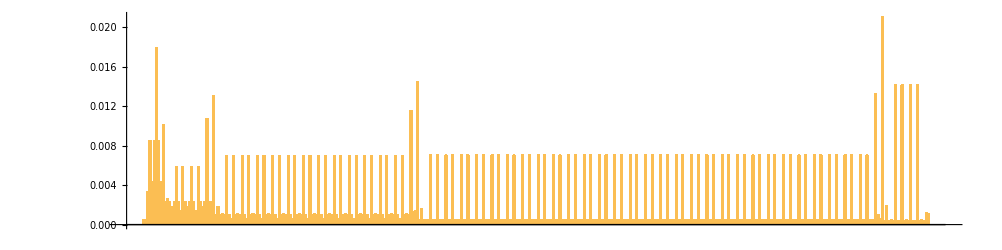

```mathematica
BarChart[vertexTimes,AspectRatio->1/4,ImageSize->Scaled[0.75]]
```

```mathematica
gr=Graph[verts,edges,GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top},EdgeShapeFunction->"Line", ImagePadding->15,VertexLabels->Placed["Name",Before],VertexShapeFunction->vertexShapes,ImageSize->{Scaled[0.75]}];
```

vertices with in degree = 1

```mathematica
inputVerts=Table[If[VertexInDegree[gr,vert]===0,vert,Nothing],{vert,VertexList[gr]}];
```

delete the input verts

```mathematica
grt=VertexDelete[gr,inputVerts];
grt=WeaklyConnectedGraphComponents[grt][[1]];
```

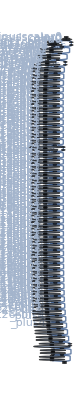

```mathematica
grt
```

## Theoretical vs CUPTI Actual for ResNet50

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
MapThread[Function[{layer,theoretical,actual},
{Tooltip[Labeled[theoretical,Style[N[actual/theoretical],Gray,FontSize->8],Above ],layer],Tooltip[actual,layer]}
],
{layerNames,theoreticalFlops,cuptiSPFlops}
]
```

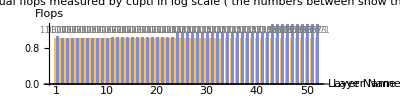

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","ResNet050-v1.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
sflopsPos=First@FirstPosition[header,"flop_count_sp"];
rows=Select[Rest[rdata],#[[2]]==="Conv"&];
theoreticalFlops=rows[[All,tflopsPos]];
cuptiSPFlops=rows[[All,sflopsPos]];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[First/@GroupBy[rows[[All,{layerNamePos,tflopsPos,sflopsPos}]],First]];
(*data[[All,1]]/=2;*)
BarChart[
plotData=MapThread[Function[{layer,theoretical,actual},
{Tooltip[Labeled[theoretical/theoretical,Style[N[actual/theoretical],Gray,FontSize->8],Above ],N[actual/theoretical]],Tooltip[actual/theoretical,layer]}
],
Prepend[Transpose@data,layerNames]
],
AxesLabel->{"Layer Name","Flops"},
(*PlotTheme->"Grid",*)
Ticks->{None,Automatic} ,
PlotLabel->"Comparison between the theortical total flops and the actual flops measured by cupti in log scale \n( the numbers between show the times different between the actual and theoretical)",
AspectRatio->1/4,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
BarSpacing->{0,1},
(*ScalingFunctions->"Log",*)
ChartLegends->{"theortical","cupti(actual)"},
ImageSize->{Scaled[0.75],Scaled[2]},
Ticks->{None,Automatic}(*,
BarOrigin->Left*)
]
```

## CUPTI Actual Decomposition for ResNet50

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

```mathematica
ClearAll[hatchF]
hatchF[mf_List:{#&,#2&},mesh_List:{50,50},style_:GrayLevel[.5],opts:OptionsPattern[]]:=ParametricPlot[{x,y},{x,0,1},{y,0,1},Mesh->mesh,MeshFunctions->mf,MeshStyle->style,BoundaryStyle->None,opts,Frame->False,PlotRangePadding->0,ImagePadding->0,Axes->False]
```

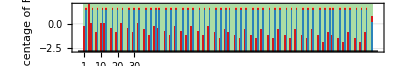

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","ResNet050-v1.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
colors={RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]};
(*colors={Black,Gray,Darker@Gray,LightGray};*)
fig=BarChart[
data,
PlotTheme->"Grid",
ChartStyle->colors,
ChartLayout->"Percentile",
AspectRatio->1/6,
BarSpacing->{0,1},
Ticks->None,
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
GridLinesStyle->Thick,
ChartElementFunction->System`BarFunctionDump`TextureBar,
ChartLabels->{Style[#,FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10]&/@Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]},
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

```mathematica
Export["/Users/abduld/Desktop/resnet50_metrics.pdf",fig,ImageSize->Scaled[1.2],ImageResolution->600]
```

/Users/abduld/Desktop/resnet50_metrics.pdf

## CUPTI Actual Decomposition for ResNet50 (Theoretical Latency) -- counts cycles

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

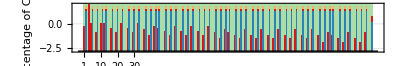

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","ResNet050-v1.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
ChartStyle->colors,
ChartLayout->"Percentile",
AspectRatio->1/6,
BarSpacing->{0,1},
Ticks->None,
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
GridLinesStyle->Thick,
ChartElementFunction->System`BarFunctionDump`TextureBar,
ChartLabels->{Style[#,FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10]&/@Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Cycles",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]},
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

```mathematica
Export["/Users/abduld/Desktop/resnet50_cycles.pdf",fig,ImageSize->Scaled[1.2],ImageResolution->600]
```

/Users/abduld/Desktop/resnet50_cycles.pdf

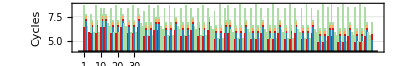

```mathematica
BarChart[
data,
PlotTheme->"Grid",
ChartStyle->colors,
ChartLayout->"Stacked",
AspectRatio->1/6,
BarSpacing->{0,1},
Ticks->None,
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
GridLinesStyle->Thick,
ChartElementFunction->System`BarFunctionDump`TextureBar,
ChartLabels->{Style[#,FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10]&/@Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameLabel->{Style["Layer Index",14],Style["Cycles",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]},
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
]
```

## CUPTI Actual Decomposition for Tiny Yolo

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

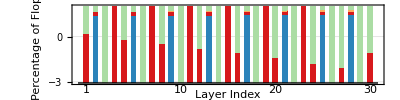

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Tiny_YOLO-v2.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for Tiny Yolo (Theoretical Latency)

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

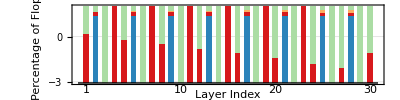

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Tiny_YOLO-v2.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for Emotion-FerPlus

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

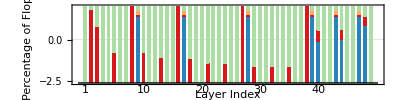

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Emotion-FerPlus.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for Emotion-FerPlus (Theoretical Latency)

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

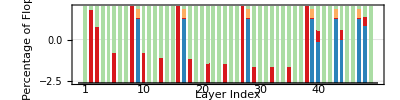

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","Emotion-FerPlus.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for DUC

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

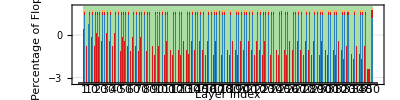

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","DUC.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## CUPTI Actual Decomposition for DUC (Theoretical Latency)

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
v100Clock=1380;
v100PeekGflop=14000;
```

```mathematica
addLatency=4;
mulLatency=4;
fmaLatency=4;
specialLatency=11;
```

```mathematica
header
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp,flops_sp_add,flops_sp_fma,flops_sp_mul,flops_sp_special,achieved_occupancy,dram_read_bytes,dram_write_bytes}

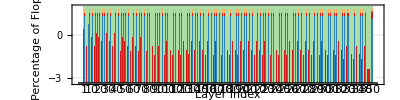

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/metrics";
rdata=Import[FileNameJoin[{dir,"batchsize_1","Tesla_V100-SXM2-16GB","DUC.csv"}],"CSV"];
header=First[rdata];
layerNamePos=First@FirstPosition[header,"LayerName"];
tflopsPos=First@FirstPosition[header,"Theoretical Flops"];
saddflopsPos=First@FirstPosition[header,"flops_sp_add"];
sfmaflopsPos=First@FirstPosition[header,"flops_sp_fma"];
smulflopsPos=First@FirstPosition[header,"flops_sp_mul"];
sspecialflopsPos=First@FirstPosition[header,"flops_sp_special"];
rows=Rest[rdata];
layerNames=DeleteDuplicates[rows[[All,layerNamePos]]];
data=Rest/@Values[Total/@GroupBy[rows[[All,{layerNamePos,saddflopsPos,smulflopsPos,sspecialflopsPos,sfmaflopsPos}]],First]];
data[[All,1]]*=addLatency;
data[[All,2]]*=mulLatency;
data[[All,3]]*=specialLatency;
data[[All,4]]*=fmaLatency;
fig=BarChart[
data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
ChartLayout->"Percentile",
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[Length[layerNames]],10]],1],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Layer Index",14],Style["Percentage of Flops",14]},
ChartLegends->Placed[{"Add","Mul","Special","FMA"},Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]
```

## Kernel Names for ResNet50 for V100

data was generated using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/v100/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=tmp.tbl --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --kernels_only=true --trim_layer_name=false

```mathematica
rawData=;
data=Rest[ImportString[rawData,"CSV"]];
```

```mathematica
layerNames=data[[All,1]];
kernelNames=Flatten[StringSplit[#,";"]]&/@data[[All,3;;]];
```

```mathematica
mapping=AssociationThread[layerNames->kernelNames];
```

```mathematica
maxColumns=Max[Length/@kernelNames]+1;
paddedList=MapThread[Module[{lst=Flatten[{#1,#2}]},PadRight[lst,maxColumns,""]]&,{layerNames,kernelNames}];
```

```mathematica
ExportString[paddedList,"CSV"]//CopyToClipboard
```

example pasted in gist https://gist.github.com/abduld/fa24725370da54905ee041d44275da15

```mathematica
Dataset[paddedList]
```

Dataset[<>]

## Theoretical vs Actual Flops for models

generate data using

go run main.go benchinfo --model_path ~/data/carml/dlperf/ --benchmark_database results/k80/profile/8.json.gz --short=false --batch_size=8 --human=false --strategy=parallel --metrics --output_file=./assets/flop_count_sp/batchsize_8/k80 --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=csv --trim_layer_name=false

```mathematica
dir="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/assets/flop_count_sp";
v100=Import[#,"CSV"]&/@FileNames["*.csv",FileNameJoin[{dir,"batchsize_1","v100"}]];
k80=Import[#,"CSV"]&/@FileNames["*.csv",FileNameJoin[{dir,"batchsize_1","k80"}]];
```

```mathematica
(FileBaseName/@FileNames["*.csv",FileNameJoin[{dir,"batchsize_1","v100"}]])[[12]]
```

MobileNet-v2

```mathematica
v100[[1,1]]
```

{LayerName,LayerType,Theoretical Flops,flop_count_sp}

```mathematica
theoreticalFlops=Total[Rest[#[[All,-2]]]]&/@k80;
```

```mathematica
v100Flops=Total[Rest[#[[All,-1]]]]&/@v100;
k80Flops=Total[Rest[#[[All,-1]]]]&/@k80;
```

```mathematica
Grid[MapThread[List,{Range[Length[k80Flops]],N[k80Flops/(1024*1024)],N[theoreticalFlops/(1024*1024)]}],Frame->All]
```

1 | 23122.7 | 20582.8
2 | 2150.86 | 2386.31
3 | 2377.45 | 2638.34
4 | 3316.21 | 6041.67
5 | 2370.88 | 2632.08
6 | 6154.08 | 5512.95
7 | 1.37235×10^6 | 1.20834×10^8
8 | 1535.02 | 1673.49
9 | 3043.27 | 5464.75
10 | 4377.57 | 3882.89
11 | 2.7493 | 1.52717
12 | 17707. | 15685.6
13 | 3888.88 | 3469.93
14 | 3890.39 | 3470.65
15 | 7849.69 | 7003.31
16 | 7851.2 | 7004.03
17 | 8458.36 | 10316.8
18 | 8881.21 | 7842.47
19 | 16668. | 20752.1
20 | 17085.5 | 14945.7
21 | 24703.4 | 31192.7
22 | 25114.7 | 22054.4
23 | 5455. | 265.868
24 | 759.017 | 1337.01
25 | 5203.97 | 6024.08
26 | 18336.2 | 58638.3
27 | 18090.7 | 58612.4
28 | 23388.3 | 74519.2
29 | 23119.2 | 74490.9
30 | 3043.29 | 5501.31

```mathematica
ExportString[MapThread[List,N@{Range[Length[k80Flops]],k80Flops/theoreticalFlops,v100Flops/theoreticalFlops,theoreticalFlops/theoreticalFlops}],"CSV"]
```

1.,1.1233985373719786,1.1252306121129703,1.
2.,0.9013336177178585,0.8745073636609445,1.
3.,0.9011159641629742,0.8769230843748765,1.
4.,0.5488895660466598,0.5548915038230001,1.
5.,0.9007610165328085,0.8766031598280664,1.
6.,1.116296319170699,1.1197414136369013,1.
7.,0.011357341455946721,0.011014349308507965,1.
8.,0.9172559980157144,0.9185421275773344,1.
9.,0.5568910929183,0.5662941682833013,1.
10.,1.127400280318708,1.1068703314436934,1.
11.,1.8002590307951896,1.8041270075198863,1.
12.,1.1288704908559513,1.114757440691444,1.
13.,1.12073758377426,1.1629858966336557,1.
14.,1.1209405296525783,1.1632352550564489,1.
15.,1.1208541435553363,1.1419152933327013,1.
16.,1.1209546956310483,1.1420410150781761,1.
17.,0.8198647221781035,0.8587303261524115,1.
18.,1.132450254355983,1.1847613819072786,1.
19.,0.8031951995765192,0.8231242345440648,1.
20.,1.1431668890653464,1.1707260358052396,1.
21.,0.7919617512546712,0.805746063834971,1.
22.,1.138762307089317,1.1575542973109523,1.
23.,20.517737745096493,19.181463432733757,1.
24.,0.5676974686573635,0.5750461073139608,1.
25.,0.8638620106843811,0.928062256875649,1.
26.,0.31270029560381357,0.39533394109112086,1.
27.,0.3086499874683109,0.39132006278128534,1.
28.,0.31385552322967897,0.39850232375939165,1.
29.,0.3103621274384002,0.3950411182713966,1.
30.,0.5531933040325133,0.5542203869091742,1.

```mathematica
ExportString[MapThread[List,{k80Flops,v100Flops,theoreticalFlops}],"CSV"]
```

24245895424,24285436416,21582630400
2255341408,2188216028,2502227104
2492935008,2426005468,2766497440
3477295530,3515318682,6335145984
2486046396,2419372160,2759940040
6453025464,6472940680,5780745984
1439014779488,1395556477972,126703488230032
1609582172,1611839046,1754779664
3191102170,3244983754,5730208672
4590213380,4506625636,4071502784
2882852,2889046,1601354
18567096712,18334972328,16447499392
4077785704,4231505512,3638483944
4079367784,4233288296,3639236584
8230997864,8385660520,7343504872
8232579944,8387443304,7344257512
8869237672,9289682984,10817928168
9312622632,9742799400,8223427560
17477615528,17911273512,21760109544
17915429928,18347330088,15671753704
25903414184,26354270248,32707910632
26334674984,26769252904,23125699560
5719985156,5347455332,278782448
795886559,806189023,1401955448
5456758628,5862292432,6316701696
19226902704,24307771140,61486679016
18969499824,24050368260,61459583976
24524384944,31138608900,78139089896
24242195120,30856419076,78109385704
3191117348,3197042116,5768539360

## ResNet50 Analysis

Generated using

go run main.go benchinfo --model_path /Users/abduld/data/carml/dlperf/ResNet50-v1/resnet50v1/resnet50v1.onnx --benchmark_database results/Tesla_V100-SXM2-16GB/profile/1.json --short=false --batch_size=1 --human=false --strategy=parallel --metrics --output_file=test.json --flops_only --flops_aggregate=true --metric_filter=flop_count_sp --total=false --format=json --trim_layer_name=fal
se

```mathematica
data=;
```

```mathematica
Keys@data[[1]]
```

{type,benchmark,flops_information}

```mathematica
Lookup[Lookup[data,"benchmark"],{"Name","Flops"}]
```

{{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__10561411637126037500<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:3/input[2]:224/input[3]:224/filter_count:64/filter_height:7/filter_width:7/pad_height:3/pad_width:3/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,118013952},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8485617627681512661<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:112/input[3]:112/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8731790411514196767<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:112/input[3]:112/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_POOLING_FWD_FLOAT32__BatchSize_1__8317600655594697260<CUDNN_POOLING_MAX>/input[0]:1/input[1]:64/input[2]:112/input[3]:112/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:2/stride_width:2/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__17452696648446571200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,12845056},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__6271735633126097759/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__1043366617614967200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__5007813973155237690/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__7147431760686454760/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__5706948421495955507<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8887210388371323745<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__16026190895114242814/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__1043366617614967200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__5007813973155237690/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__7147431760686454760/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__5706948421495955507<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8887210388371323745<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__16026190895114242814/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:64/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__1043366617614967200<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:64/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__12739174055704890753<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__13557477638093759051<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__16159642449668292261<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__5007813973155237690/input[0]:1/input[1]:64/input[2]:56/input[3]:56/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__4889873461955448825<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__7147431760686454760/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__5706948421495955507<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,802816},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__2698634678934534712<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,25690112},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__9245529975646030759/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9900471406965659822<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:56/input[3]:56/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,102760448},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__242870976285140334<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__11989453759287694577/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__242870976285140334<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__11989453759287694577/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__242870976285140334<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__11989453759287694577/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:128/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__4351453730202563248<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:128/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8576969857009013610<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8928652341575007392<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__7798876574900765510<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__14485526500804768473/input[0]:1/input[1]:128/input[2]:28/input[3]:28/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__8360591339321800497<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__6118805117996298016/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__8712702611812473083<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,401408},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__5696751150347348050<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,25690112},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__16875882305802639821/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__2863503841521678117<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:28/input[3]:28/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,102760448},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__8357479253003863531<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15476191789384529012/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:256/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__6082869558800079188<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:256/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__941175568489382689<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__135336045844557035<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,50176},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__13877788952103163203<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__7325684169354896604/input[0]:1/input[1]:256/input[2]:14/input[3]:14/filter_count:1024/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__3630124348827013261<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__1336548246304966812/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__4508032340183514951<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,200704},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__10645803091547187777<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,25690112},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__3927346633012288478/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__11471501776210827496<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:512/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9186393106048364330<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15726955474433007285/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__10357631549930852067<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:1024/input[2]:14/input[3]:14/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:2/stride_width:2/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,102760448},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__8521853693205159583/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__6503291060933470532<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9173660249711801802<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15740821849914442837/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__11471501776210827496<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:512/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9186393106048364330<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15726955474433007285/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__8521853693205159583/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__6503291060933470532<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9173660249711801802<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15740821849914442837/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/filter_count:512/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__11471501776210827496<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:512/filter_height:3/filter_width:3/pad_height:1/pad_width:1/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,115605504},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__15374206207229039173<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__15686972418460941711<CUDNN_ACTIVATION_CLIPPED_RELU>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,25088},{LAYER_CUDNN_CONV_FWD_FLOAT32__BatchSize_1__9186393106048364330<CUDNN_CONVOLUTION_FWD_ALGO_IMPLICIT_GEMM>/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:1/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,51380224},{LAYER_CUDNN_ADD_TENSOR_FLOAT32__BatchSize_1__15726955474433007285/input[0]:1/input[1]:512/input[2]:7/input[3]:7/filter_count:2048/filter_height:1/filter_width:1/pad_height:0/pad_width:0/stride_height:1/stride_width:1/dilation_height:1/dilation_width:1/conv_fwd_type:2/conv_bwd_type:0/batch_size:1/group:1/iterations:10/manual_time,Null},{LAYER_CUDNN_BATCHNORM_FWD_INFERENCE_FLOAT32__BatchSize_1__6246248146433820302<CUDNN_BATCHNORM_PER_ACTIVATION>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUDNN_OP_TENSOR_ADD_FWD_FLOAT32__BatchSize_1__8521853693205159583/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,Null},{LAYER_CUDNN_ACTIVATION_FWD_FLOAT32__BatchSize_1__6503291060933470532<CUDNN_ACTIVATION_RELU>/input[0]:1/input[1]:2048/input[2]:7/input[3]:7/input[4]:-1/input[5]:-1/input[6]:-1/input[7]:-1/batch_size:1/iterations:10/manual_time,100352},{LAYER_CUBLAS_GEMV_FWD_FLOAT32__BatchSize_1__1841169376419394758/input[0]:1000/input[1]:2048/input[2]:1/input[3]:1/input[4]:1/input[5]:-1/input[6]:0/input[7]:0/batch_size:1/iterations:10/manual_time,2048000}}

## MXNet Padding Overhead

```mathematica
profile=Import["/tmp/e.json","RawJSON"]["traceEvents"];
```

```mathematica
gpuPid=SelectFirst[profile,Lookup[Lookup[#,"args",<||>],"name",None]==="gpu/0"&]["pid"]
```

8

```mathematica
allTimeSpans=Select[profile,Lookup[#,"pid"]==gpuPid&&KeyExistsQ[#,"ts"]&];
padTimeSpans=Select[profile,Lookup[#,"name"]==="Pad"&&Lookup[#,"pid"]==gpuPid&];
```

```mathematica
allTime=N@Total[
MapThread[
#2["ts"]-#1["ts"]&,
Transpose[Partition[allTimeSpans,2]]
]
]
```

171730.

```mathematica
padTime=N@Total[
MapThread[
#2["ts"]-#1["ts"]&,
Transpose[Partition[padTimeSpans,2]]
]
]
```

1010.

```mathematica
padTime/allTime
```

0.0639119

## Onnx Runtime Results

```mathematica
Manipulate[
Module[{},
batchSize=ToString[bs];
csvFiles=FileNames["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/*_"<>batchSize<>".csv"];
data=Association[Table[
name=StringTrim[FileBaseName[file],"_"<>batchSize];
content=Import[file,"Text"];
content=StringRiffle[Select[StringSplit[content,"\n"],StringMatchQ[#,StartOfString~~DigitCharacter..~~","~~___]&],"\n"];
content=ImportString[content,"CSV"];
content=AssociationThread[content[[All,1]]->content[[All,2;;]]];
name->content
,{file,csvFiles}
]];
data2=data;
data=Table[Last[Lookup[#,model,{0}]]&/@data,{model,Range[0,29]}];
BarChart[Values/@data,
PlotTheme->"Grid",
Ticks->None,
ChartStyle->{RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]},
AspectRatio->1/4,
BarSpacing->{0,1},
Frame->{False,True,False,True},
Axes->{True,False},
ScalingFunctions->"Log10",
PlotRangePadding->None,
FrameTicksStyle->{Thick,None},
BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
GridLinesStyle->Thick,
ChartLabels->{Prepend[Flatten[Append[ConstantArray["",Length[Most[#]]],Last[#]]&/@Partition[Range[0,29],5]],0],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Model Index",14],Style["Latency",14]},
ChartLegends->Placed[Keys[data[[1]]],Above],
ImageSize->{Scaled[0.75],Scaled[2]}
]],
{bs,2^Range[0,8]}
]
```

```mathematica
data2["mxnet"][14]
```

{ResNet034-v1,290.773}

```mathematica
data[[16]]
```

<|caffe2→5.82931,mxnet→3.67742,onnxruntime→3.86598|>

## ResNet 34-v1

```mathematica
model=15;
batchSizes=2^Range[0,8];
```

```mathematica
ts=Association@Table[
batchSize=ToString[bs];
csvFiles=FileNames["/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/onnx_examples/results/*_"<>batchSize<>".csv"];
data=Association[Table[
name=StringTrim[FileBaseName[file],"_"<>batchSize];
content=Import[file,"Text"];
content=StringRiffle[Select[StringSplit[content,"\n"],StringMatchQ[#,StartOfString~~DigitCharacter..~~","~~___]&],"\n"];
content=ImportString[content,"CSV"];
content=AssociationThread[content[[All,1]]->content[[All,2;;]]];
name->content
,{file,csvFiles}
]];
data2=data;
data=Last[Lookup[#,model,{0}]]&/@data;
bs->data,
{bs,batchSizes}
];
```

```mathematica
frameworks=Keys[ts[1]]
```

{caffe2,mxnet,onnxruntime}

```mathematica
ts
```

<|1→<|caffe2→5.43201,mxnet→3.25832,onnxruntime→3.45395|>,2→<|caffe2→5.82931,mxnet→3.67742,onnxruntime→3.86598|>,4→<|caffe2→6.57687,mxnet→4.60899,onnxruntime→4.76716|>,8→<|caffe2→9.99315,mxnet→7.93002,onnxruntime→8.27951|>,16→<|caffe2→15.6991,mxnet→12.1723,onnxruntime→13.7484|>,32→<|caffe2→27.6339,mxnet→21.498,onnxruntime→26.7169|>,64→<|caffe2→45.2183,mxnet→44.8094,onnxruntime→70.7363|>,128→<|mxnet→88.1913,onnxruntime→91.4276|>,256→<|mxnet→171.436,onnxruntime→276.004|>|>

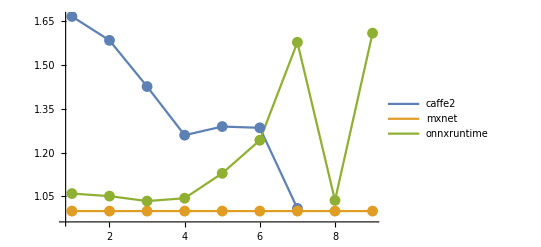

```mathematica
ListLinePlot[
Table[
Lookup[ts[bs],framework]/Lookup[ts[bs],"mxnet"]
,
{framework,frameworks},
{bs,batchSizes}
],
Mesh->All,
PlotRange->Full,
(*ScalingFunctions->"Log2",*)
PlotLegends->frameworks,
ImageSize->Scaled[0.75]
]
```

## Batch Optimization

finding the best convolution parameters / decomposition.

when we see a conv layer, we find the best entry in the database that matches its dimensions.
But this may not be the fastest way to run the convolution algorithm.

conv = find[NHWC]=2 find[N/2 HWC]

## Layer Unique % per Year Results

```mathematica
inputFile="/Users/abduld/.gvm/pkgsets/go1.12/global/src/github.com/rai-project/dlperf/results/layers_per_year.json";
rdata=Import[inputFile,"RawJSON"];
```

```mathematica
colors={RGBColor[0.16862745098039217, 0.5137254901960784, 0.7294117647058823],RGBColor[0.8431372549019608, 0.09803921568627451, 0.10980392156862745],RGBColor[0.9921568627450981, 0.6823529411764706, 0.3803921568627451],RGBColor[0.6705882352941176, 0.8666666666666667, 0.6431372549019608]};
colors={Black,Gray};
```

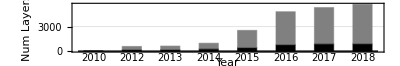

```mathematica
fig=Legended[
BarChart[
Transpose[{
Lookup[rdata,"unique"],
Lookup[rdata,"total"]-Lookup[rdata,"unique"]
}],
ChartLayout->"Stacked",
PlotTheme->"Grid",
Ticks->None,
ChartStyle->colors,
AspectRatio->1/6,
BarSpacing->{0,1},
Axes->{True,False},
(*ScalingFunctions->"Log10",*)
PlotRangePadding->None,
BaseStyle->{FontFamily->"Arial",FontColor->Black,FontSize->10},
ImageMargins->0,
Frame->True,
ChartLabels->{Style[#,FontFamily->"Arial",FontColor->Black,FontSize->10]&/@Lookup[rdata,"year"],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Year",14],Style["Num Layers",14]},
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10}
],
Placed[SwatchLegend[colors,Style[#,FontFamily->"Latin Modern Roman",FontSize->14]&/@{"Unique","Duplicate"},Background->Opacity[0.6,White],LegendLayout->"Row",LegendMarkerSize->10,LegendMargins->0,LabelStyle->{FontFamily->"Latin Modern Roman"}],{{0.6,0.95},{2.8,0.9}}]
]
```

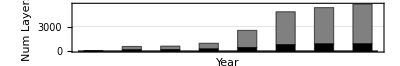

```mathematica
fig=BarChart[
Transpose[{
Lookup[rdata,"unique"],
Lookup[rdata,"total"]-Lookup[rdata,"unique"]
}],
ChartLayout->"Stacked",
PlotTheme->"Grid",
Ticks->None,
ChartStyle->colors,
AspectRatio->1/6,
BarSpacing->{0,1},
Axes->{True,False},
(*ScalingFunctions->"Log10",*)
PlotRangePadding->None,
ImageMargins->0,
Frame->True,
ChartLabels->{Style[#,FontFamily->"Arial",FontColor->Black,FontSize->10]&/@Lookup[rdata,"year"],None},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{Style["Year",14],Style["Num Layers",14]},
ImageSize->Scaled[0.75],
FrameStyle->Directive[AbsoluteThickness[0.5],GrayLevel[0]],
BaseStyle->{FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->10},
ChartLegends->Placed[SwatchLegend[colors,Style[#,FontFamily->"Latin Modern Roman",FontSize->14]&/@{"Unique","Duplicate"},Background->Opacity[0.6,White],LegendLayout->"Row",LegendMarkerSize->10,LegendMargins->0,LabelStyle->{FontFamily->"Latin Modern Roman"}],Above],
TicksStyle->{Opacity@0,Automatic},
LabelStyle->Opacity[1]
]
```

```mathematica
Export["/Users/abduld/Desktop/unique_layer_year.pdf",fig,ImageSize->Scaled[1.2],ImageResolution->600]
```

/Users/abduld/Desktop/unique_layer_year.pdf

## Looking at Transformer Networks

```mathematica
gpt=NetFlatten@NetModel["GPT Transformer Trained on BookCorpus Data"];
gpt2=NetFlatten@NetModel["GPT-2 Transformer Trained on WebText Data"];
bert=NetFlatten@NetModel["BERT Trained on BookCorpus and English Wikipedia Data"];
```

```mathematica
ClearAll[proc,trimArraysConstant,inputs,inputs0];
trimArraysConstant[assoc0_]:=Module[{assoc=assoc0,arrays},
If[KeyExistsQ[assoc,"Arrays"],
arrays=Lookup[assoc,"Arrays"];
If[KeyExistsQ[arrays,"Scaling"],
AssociateTo[arrays,"Scaling"->Dimensions[Lookup[arrays,"Scaling"]]]
];
If[KeyExistsQ[arrays,"Weights"],
AssociateTo[arrays,"Weights"->Dimensions[Lookup[arrays,"Weights"]]]
];
If[KeyExistsQ[arrays,"Biases"],
AssociateTo[arrays,"Biases"->Dimensions[Lookup[arrays,"Biases"]]]
];
AssociateTo[assoc,"Arrays"->arrays];
assoc
]
];
proc[lyr_[assoc0_,r___]]:=Module[{assoc=assoc0,trimArrys,arrays,params,net},
If[KeyExistsQ[assoc,"Arrays"],
AssociateTo[assoc,"Arrays"->trimArraysConstant[Lookup[assoc,"Arrays"]]]
];
If[KeyExistsQ[assoc,"Parameters"]&&KeyExistsQ[Lookup[assoc,"Parameters"],"Arrays"],
AssociateTo[assoc,"Parameters"->Append[Lookup[Lookup[assoc,"Parameters"],"Arrays"],"Arrays"->trimArraysConstant[Lookup[Lookup[assoc,"Parameters"],"Arrays"]]]]
];
If[KeyExistsQ[assoc,"Parameters"]&&KeyExistsQ[Lookup[assoc,"Parameters"],"Net"],
params=Lookup[assoc,"Parameters"];
net=Lookup[params,"Net"];
If[KeyExistsQ[net,"Arrays"],
AssociateTo[net,"Arrays"->trimArraysConstant[Lookup[net,"Arrays"]]];
];
AssociateTo[params,"Net"->net];
AssociateTo[assoc,"Parameters"->params]
];
(*KeyDropFrom[assoc,"Inputs"];
KeyDropFrom[assoc,"Output"];*)
Inactive[lyr][assoc,r]
];
proc[atom_]:=
With[{hd=ToString[Head[atom]]},
proc@ToExpression[StringReplace[ToBoxes[InputForm@atom][[1,1]],hd->ToLowerCase[hd]]]
];
inputs0[lyr_[assoc_,___]]:=Module[{in=Values@Lookup[assoc,"Inputs"]},
in//.{
NeuralNetworks`TensorT[x___]:>{x},
NeuralNetworks`IndexIntegerT[x_]:>x,
NeuralNetworks`LengthVar[x_]:>x
}
];
inputs[lyr_[assoc_,___]]:=Module[{in=Lookup[assoc,"Inputs"]},
in
]
```

```mathematica
bertLyrs=NetExtract[bert,All];
bertLyrsProc=proc/@Values[bertLyrs];
bertLyerIns=inputs/@bertLyrsProc;
```

```mathematica
gptLyrs=NetExtract[gpt,All];
gptLyrsProc=proc/@Values[gptLyrs];
gptLyerIns=inputs/@gptLyrsProc;
```

```mathematica
gpt2Lyrs=NetExtract[gpt2,All];
gpt2LyrsProc=proc/@Values[gpt2Lyrs];
gpt2LyerIns=inputs/@gpt2LyrsProc;
```

```mathematica
Length[Join[bertLyrsProc,gptLyrsProc,gpt2LyrsProc]]
```

2551

```mathematica
Length[Union[Join[bertLyrsProc,gptLyrsProc,gpt2LyrsProc]]]
```

48

```mathematica
48./2551
```

0.0188162

```mathematica
N[Length[Union[gpt2LyrsProc]]/Length[gpt2LyrsProc]]
```

0.0168269

```mathematica
Length[Union[plyrs]]
```

19

```mathematica
lyrs//Length
```

862

```mathematica
Activate[lyrs[[20]]]
```

AttentionLayer[<>]

```mathematica
NetModel["GPT Transformer Trained on BookCorpus Data","ParametersInformation"]
```

```mathematica
lm=NetModel[{"GPT Transformer Trained on BookCorpus Data","Task"->"FeatureExtraction"}]
```

NetChain[<>]

```mathematica
NetInformation[Activate[lyrs[[20]]],"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

```mathematica
input=<|"Key"->RandomReal[1,{10,64}],"Value"->RandomReal[1,{10,64}],"Query"->RandomReal[1,{10,64}]|>;
lyr=Activate[lyrs[[20]]];
```

```mathematica
RepeatedTiming[ lyr[input];]
```

{0.00043,Null}

```mathematica
proc[lyrs[[20]]]
```

AttentionLayer[<|Type→Attention,Arrays→Null,Parameters→<|ScoringNet→<|Type→Graph,Inputs→<|Query→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT],Input→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{},NeuralNetworks`RealT]|>,Nodes→<|1→<|Type→Dot,Arrays→<||>,Parameters→<||>,Inputs→<|1→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT],2→NeuralNetworks`TensorT[{64},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{},NeuralNetworks`RealT]|>|>|>,Edges→{NeuralNetworks`NetPath[Nodes,1,Inputs,1]→NeuralNetworks`NetPath[Inputs,Query],NeuralNetworks`NetPath[Nodes,1,Inputs,2]→NeuralNetworks`NetPath[Inputs,Input],NeuralNetworks`NetPath[Outputs,Output]→NeuralNetworks`NetPath[Nodes,1,Outputs,Output]}|>,Mask→None,ScoreRescaling→None,$InputPorts→KeyValueQuery,$InputShape→{NeuralNetworks`LengthVar[1234191656]},$QueryShape→{NeuralNetworks`LengthVar[1234191656]},$QueryChannels→{64},$KeyChannels→{64},$ValueChannels→{64}|>,Inputs→<|Key→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT],Value→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT],Query→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT]|>,Outputs→<|Output→NeuralNetworks`TensorT[{NeuralNetworks`LengthVar[1234191656],64},NeuralNetworks`RealT]|>|>,<|Version→12.0.12,Unstable→False|>]

## Hatched BarChart

https://mathematica.stackexchange.com/questions/34035/hatched-bars-and-bar-specific-background-in-barchart

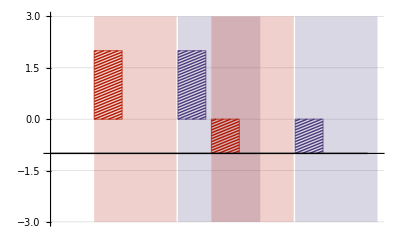

```mathematica
barFilled[gap_,h_,seg_][{{xmin_,xmax_},{ymin_,ymax_}},___]:=Module[{width,line,yt,yb,lend},{yb,yt}=Sort[{ymin,ymax}];
width=xmax-xmin;
line=Table[{{xmin,i},{xmax,i+width}},{i,yb,yt-width,h/seg}];
lend=line[[-1,1,2]];
line={Line[line],Line[Table[{{xmin+i,yb},{xmax,yb+width-i}},{i,h/seg,width,h/seg}]],Line[Table[{{xmin,lend+i},{xmax-(lend+width-yt)-i,yt}},{i,h/seg,width+h/seg,h/seg}]]};
{{Opacity[.2],EdgeForm[],Rectangle[{xmin,-h},{xmax+gap,h}]},{CapForm["Butt"],line},{FaceForm[],Rectangle[{xmin,ymin},{xmax,ymax}]}}]

BarChart[{{2,2},{-1,-1}},BarSpacing->2,ChartElementFunction->barFilled[.65,3,35],ChartStyle->61,GridLines->{None,Automatic}]
```

https://mathematica.stackexchange.com/questions/31221/how-do-i-plot-a-histogram-with-hatched-shading

Nearest::nearuf: The user-supplied distance function If[#2-#1>0,#2-#1,$MaxMachineNumber]& does not give a real numeric distance when applied to the point pair 2 Automatic and -23/5.

Nearest::near1: DistanceFunction→(If[#2-#1>0,#2-#1,$MaxMachineNumber]&) is neither a list of real points nor a valid list of rules.

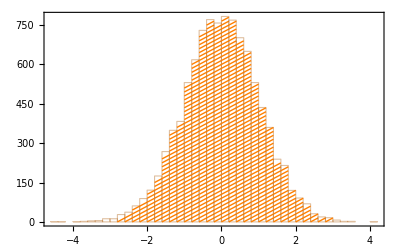

```mathematica
g[{{xmin_,xmax_},{ymin_,ymax_}},___]:=Module[{yval,line},yval=Range[ymin,ymax,15];
line=Line/@Transpose@{Most@({xmin,#}&/@yval),Rest@({xmax,#}&/@yval)};
{FaceForm[White],Polygon[{{xmin,ymin},{xmax,ymin},{xmax,ymax},{xmin,ymax}}],Orange,line}];
T=RandomVariate[NormalDistribution[0,1],10000];
Histogram[T,30,ChartElementFunction->g,ChartBaseStyle->EdgeForm[{Thin,Darker@Orange}],Frame->True]
```

Nearest::nearuf: The user-supplied distance function If[#2-#1>0,#2-#1,$MaxMachineNumber]& does not give a real numeric distance when applied to the point pair 2 Automatic and -4.

Nearest::near1: DistanceFunction→(If[#2-#1>0,#2-#1,$MaxMachineNumber]&) is neither a list of real points nor a valid list of rules.

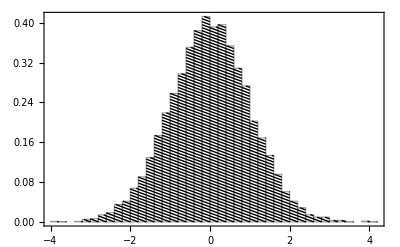

```mathematica
g[step_?NumberQ][{{xmin_,xmax_},{ymin_,ymax_}},___]:=Module[{yval,lines,xstart,xend},yval=Range[ymin,ymax,Abs[step]];
If[step>0,{xstart,xend}={xmin,xmax},{xstart,xend}={xmax,xmin}];
lines=Transpose@{{xstart,#}&/@Most[yval],{xend,#}&/@Rest[yval]};
lines=Join[lines,{{{xstart,Last@yval},{xstart+((xend-xstart) (ymax-Last@yval))/Abs[step],ymax}}}];
{FaceForm[None],Rectangle[{xmin,ymin},{xmax,ymax}],CapForm["Butt"],Line[lines]}];
data=RandomVariate[NormalDistribution[0,1],10000];
Histogram[data,30,"PDF",ChartElementFunction->g[-.006],ChartBaseStyle->{Directive[{EdgeForm[{Thin,Black}],Black}]},Frame->True]
```